## Run all this first

```mathematica
$HistoryLength=0;
```

## Package ODE

```mathematica
PacletDirectoryAdd["~/github/EcoEvo"];
```

PacletDirectoryAdd::expobs: The experimental function PacletDirectoryAdd is now obsolete and is superseded by PacletDirectoryLoad.

PacletDirectoryLoad::nodir: Directory /Users/nassermohammed/github/EcoEvo not found.

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.6.4 (November 5, 2021)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
SetModel[{
Pop[n1]->{Equation:> r1 n1(1-(n1+α12 n2)/k1)+m1(nr1-n1),Color->Blue},
Pop[n2]->{Equation:> r2 n2(1-(n2+α21 n1)/k2)+m2(nr2-n2),Color->Red},
Parameters:>{r1>=0,r2>=0,α12,α21,m1>=0,m2>=0}
}]
```

```mathematica
m1=m2=0;
eq=SolveEcoEq[]
```

{{n1→0,n2→0},{n1→k1,n2→0},{n1→0,n2→k2},{n1→-(k1-k2 α12)/(-1+α12 α21),n2→-(k2-k1 α21)/(-1+α12 α21)}}

```mathematica
Clear[m1,m2]
```

## Helper Functions

```mathematica
SetSystemOptions["SparseArrayOptions"->"TreatRepeatedEntries"->Total];
```

### InterpolationToPiecewise

```mathematica
InterpolationToPiecewise[if_,x_]:=Module[{main,default,grid},grid=if["Grid"];
Piecewise[{if@"GetPolynomial"[#,x-#],x<First@#}&/@grid[[2;;-2]],if@"GetPolynomial"[#,x-#]&@grid[[-1]]]]/;if["InterpolationMethod"]=="Hermite"
```

### fx

```mathematica
fx[x_]:=If[x<1,N[x],IntegerPart[x]];
```

### restylePlot

```mathematica
restylePlot[plot_Graphics,styles_List,op:OptionsPattern[Graphics]]:=Module[{x=styles},Show[MapAt[#/.{__,ln__Line}:>{Directive@Last[x=RotateLeft@x],ln}&,plot,1],op]]
```

### ConstantCoefficient

```mathematica
(* based on <https://mathematica.stackexchange.com/a/83404/6358> by MichaelE2 *)
ClearAll[ConstantCoefficient];ConstantCoefficient[list_List,form_]:=(ConstantCoefficient[#,form])&/@list;
ConstantCoefficient[expr_,form_]:=If[expr=!=0,Flatten[CoefficientList[expr,form]]⟦1⟧,0];
```

### GillespieSSA

```mathematica
ClearAll[GillespieSSA];
GillespieSSA[proc_List,ics:({__Rule}|_Association),{mint_?NumberQ,maxt_?NumberQ},opts___?OptionQ]:=
Module[{
(* options *)
maxsteps,dstep,debug,
(* other variables *)
in,vars,initialValues,rates,rules,null,a,b,symRates,rep,stepList,step,compiled,times,rest},

(* parse options *)
maxsteps=Evaluate[MaxSteps/.Flatten[{opts,Options[GillespieSSA]}]];
dstep=Evaluate[DStep/.Flatten[{opts,Options[GillespieSSA]}]];
debug=Evaluate[Debug/.Flatten[{opts,Options[GillespieSSA]}]];

(*Pre-generating a list is much faster than iteratively calling one-by-one.*)stepList=N@RandomVariate[ExponentialDistribution@1,maxsteps+1];

in=Normal[ics]; (* convert Association to Rules *)

vars=in⟦All,1⟧;
If[debug,Print["vars=",vars]];
initialValues=in⟦All,2⟧;

(* transition rules *)
rules=proc⟦All,1⟧;
If[debug,Print["rules=",rules]];

(* rates *)
rates=proc⟦All,2⟧;
If[debug,Print["rates=",rates]];

(* convert transition rules into a matrices and b vectors (count=a.count+b) for each transition *)
null=Table[var->var,{var,vars}]; (* null transitions don't need to be specified in proc *)
a=Table[Table[Coefficient[Table[var′/.Join[rule,null],{var′,vars}],var],{var,vars}],{rule,rules}];
If[debug,Print["a=",a]];
b=Table[ConstantCoefficient[vars/.Join[rule,null],vars],{rule,rules}];
If[debug,Print["b=",b]];

Block[{count},
rep=Thread[vars->Table[Indexed[count,i],{i,Length@vars}]];
symRates=rates/.rep;
compiled=ReleaseHold[Hold@Compile[{{init,_Integer,1},{aa,_Integer,3},{bb,_Integer,2},{dtList,_Real,1},{min,_Real},{max,_Real},{iter,_Integer},{resol,_Integer}},Module[{count=init,rates,i=1,c=1,t=min,dt,range,r,rateSum,data=Internal`Bag[]},
rates="SymbolicRates";
rateSum=N@Total@rates;
range=Range@Length@rates;
Internal`StuffBag[data,Internal`Bag[Join[{t},N@count]]];

While[rateSum>0.&&t<max&&i≤iter,
i++;
dt=dtList⟦i⟧/rateSum; (* time step *)
t=Min[max,t+dt]; (* advance t *)
If[Mod[i,resol]==0, (* store data *)
c++;
Internal`StuffBag[data,Internal`Bag[Join[{t},N@count]]];
];
r=RandomChoice[rates->range]; (* pick an event, weighted by rates *)
count=Max[0,#]&/@(aa⟦r⟧.count+bb⟦r⟧); (* update population vector "count" based on reaction #r *)
rates="SymbolicRates"; (* update rates *)
rateSum=N@Total@rates (* update total rate *)
];

(* store last data point *)
If[Mod[i,resol]≠0||(t<max&&i<iter),
c++;
Internal`StuffBag[data,Internal`Bag[Join[{max},N@count]]]
];

(* unbag results into a table *)
Table[Internal`BagPart[Internal`BagPart[data,j],All],{j,c}]
],
Parallelization->True,RuntimeAttributes->Listable,RuntimeOptions->"Speed",CompilationOptions->{"InlineExternalDefinitions"->True,"InlineCompiledFunctions"->True}]/."SymbolicRates"->symRates];

(* call compiled function *)
{times,rest}={First@#,Rest@#}&@Transpose@compiled[Round@initialValues,Round@a,Round@b,N@stepList,N@mint,N@maxt,Round@maxsteps,dstep];

(* convert results to InterpolatingFunctions *)
Thread[vars->(Interpolation[Transpose@{times,#},InterpolationOrder->0]&/@rest)]
]];

Options[GillespieSSA]={MaxSteps->10^7,DStep->1,Debug->False};

(* alias to omit mint *)
GillespieSSA[proc_List,ics:({__Rule}|_Association),maxt_?NumberQ,opts___?OptionQ]:=GillespieSSA[proc,ics,{0,maxt},opts];

GillespieSSA::usage="GillespieSSA[proc,ics,tmax] simulates process proc, with initial conditions ics, up to time tmax.";
```

### plot3dopts

```mathematica
plot3dopts={AxesLabel->{Text[Style["N_1",22,Bold]],Text[Style["N_2",22,Bold]],Text[Style["P  ",22,Bold]]},AxesStyle->Directive[18,Bold,Thick],ImageSize->Large};
```

### listAppend

```mathematica
listAppend[list1_List,list2_List]:=Table[Append[list1⟦x⟧,list2⟦x⟧],{x,Length[list1]}]
```

### TotalBy

```mathematica
(* based on Mr.Wizard <https://mathematica.stackexchange.com/a/61674/6358> *)
TotalBy[list_List,class_List]:=Merge[Thread[#2->#&@@{Flatten[list],Flatten[class]}],Total]
```

### SquarePieChart

```mathematica
Clear[SquarePieChart];
SquarePieChart[fracs_,opts___?OptionQ]:=PieChart[fracs,opts,PlotRange->{{-0.1,0.1},{-0.1,0.1}}];
```

### DrawPatch

```mathematica
Clear[DrawPatch];
DrawPatch[rules_,center_:{0,0},rad_:0.5]:=Graphics[Evaluate[{
{Gray,Disk[center,rad]},
{Black,Circle[center,rad]},
If[n1>0,{Blue,PointSize[0.015*rad],Point[RandomPoint[Disk[center,0.96rad],n1]]}],
If[n2>0,{Red,PointSize[0.015*rad],Point[RandomPoint[Disk[center,0.96rad],n2]]}]
}/.rules]]
```

```mathematica
(*Clear[DrawPatch];
DrawPatch[rules_]:=Graphics[Evaluate[{
{Black,Circle[{0,0},1]},
If[n1>0,{Text["🐷",#]&/@RandomPoint[Disk[{0,0},0.98],n1]}],
If[n2>0,{Text["🐧",#]&/@RandomPoint[Disk[{0,0},0.98],n2]}]
}/.rules]]*)
```

```mathematica
(*Clear[DrawPatch];
points=RandomPoint[Disk[{0,0},0.98],300];
DrawPatch[rules_]:=Graphics[Evaluate[{
{Black,Circle[{0,0},1]},
If[n1>0,{Text["🐷",#]&/@points[[1;;n1]]}],
If[n2>0,{Text["🐧",#]&/@points[[n1+1;;n1+n2]]}]
}/.rules]]*)
```

### DeleteRowAndColumn

```mathematica
DeleteRowAndColumn[M_,x_]:=Transpose[Delete[Transpose[Delete[M,x]],x]];
```

## Fortran Stuff

```mathematica
SetDirectory[NotebookDirectory[]<>"/fortran"]
```

SetDirectory::cdir: Cannot set current directory to /Users/nassermohammed/Documents/KlausmeierLab/Projects/LV_migration//fortran.

$Failed

```mathematica
tend:=Floor[tmax/tskip]
```

```mathematica
p[t_Integer]:=pdat⟦t+1⟧
```

### WriteList

```mathematica
WriteList[strm_,list_List]:=Module[{},Do[Write[strm,list[[i]]//FortranForm],{i,1,Length[list]}]];
```

### RunSim / RunSimLSODES

```mathematica
RunSim:=Module[{stream,tmp},
stream=OpenWrite["input"];
WriteList[stream,{r1,r2,k1,k2,α12,α21,i1,i2,m1,m2,e}];
WriteList[stream,{n1max,n2max,tskip,tmax}];
WriteList[stream,{rtol,atol,mf,ml,mu}];
Do[
Do[
Write[stream,pinit[n1,n2]//FortranForm];
,{n1,0,n1max}]
,{n2,0,n2max}];
Close[stream];
Clear[stream];

Run["rm output"];

PrintTemporary["running simulation..."];

Print["time=",AbsoluteTiming[Run["./mc21 < input"]]⟦1⟧," s"];

PrintTemporary["reading data..."];

tmp=ReadList["!grep -v 't=' output",Number];

PrintTemporary["refurbishing data..."];

pdat=ArrayReshape[tmp,{tend+1,(n1max+1)*(n2max+1)}];

slist=ReadList["!cut -b18-25 messages",Number];

(*Clear[dat];*)

];
```

```mathematica
RunSimLSODES:=Module[{stream,tmp},
stream=OpenWrite["input"];
WriteList[stream,{r1,r2,k1,k2,α12,α21,i1,i2,m1,m2,e}];
WriteList[stream,{n1max,n2max,tskip,tmax}];
WriteList[stream,{rtol,atol,121,20(n1max+1)(n2max+1)}];
Do[
Do[
Write[stream,pinit[n1,n2]//FortranForm];
,{n1,0,n1max}]
,{n2,0,n2max}];
Close[stream];
Clear[stream];

Run["rm output"];

PrintTemporary["running simulation..."];

Print["time=",AbsoluteTiming[Run["./mc21lsodes < input"]]⟦1⟧," s"];

PrintTemporary["reading data..."];

tmp=ReadList["!grep -v 't=' output",Number];

PrintTemporary["refurbishing data..."];

pdat=ArrayReshape[tmp,{tend+1,(n1max+1)*(n2max+1)}];

slist=ReadList["!cut -b18-25 messages",Number];

(*Clear[dat];*)

];
```

### ArchiveSim

```mathematica
ArchiveSim[notes_]:=Module[{stream,datestamp},
datestamp=ToString[Round[FromDate[Date[]]]];
Run["compress < input > input_"<>datestamp<>".Z"];
Run["compress < output > output_"<>datestamp<>".Z"];
Run["compress < messages > messages_"<>datestamp<>".Z"];
stream=OpenAppend["archives.txt"];
WriteString[stream,datestamp<>" "<>notes<>"\n"];
Close[stream];Clear[stream];
];
```

## Main Functions

### Usage messages

```mathematica
Setnmax::usage="Setnmax[n1max,n2max] sets n1max & n2max and everything that depends on them.  Be sure to run whenever you change either.";
```

```mathematica
GetDis1::usage="GetDis1[im1] solves for the n1-only stationary distribution given immigration rate im1.";
GetDis2::usage="GetDis2[im2] solves for the n2-only stationary distribution given immigration rate im2.";
GetDis::usage="GetDis[{im1,im2}] solves for the two-species stationary distribution given immigration rates im1 and im2.";
```

```mathematica
GetNr1::usage="GetIm1[dis] adds up n1-immigrants out of the single-species distribution dis.";
GetNr2::usage="GetIm2[dis] adds up n2-immigrants out of the single-species distribution dis.";
GetNr2::usage="GetIm[dis] adds up n1- and n2-immigrants out of the two-species distribution dis.";
```

```mathematica
NrInOut1::usage="ImInOut1[im1] calculates n1-immigrants out, given im1 immigrants in.";
NrInOut2::usage="ImInOut2[im2] calculates n2-immigrants out, given im2 immigrants in.";
NrInOut::usage="ImInOut[{im1,im2}] calculates n1- and n2-immigrants out, given im1 and im2 immigrants in.";
```

```mathematica
Eq1::usage="Eq1 finds an n1-only equilibrium.";
Eq2::usage="Eq2 finds an n2-only equilibrium.";
Eq12::usage="Eq12 finds a two-species equilibrium.";
```

```mathematica
Inv1::usage="Inv1[im2] calculates the invasion rate of n1 given n2 immigration rate of im2."; 
Inv2::usage="Inv2[im1] calculates the invasion rate of n2 given n1 immigration rate of im1.";
```

```mathematica
TM1::usage="TM1[im1] makes the n1-only transition matrix given n1 immigration rate im1.";
TM2::usage="TM2[im2] makes the n2-only transition matrix given n2 immigration rate im2.";
TM::usage="TM[im1,im2] makes the two-species transition matrix given mmigration rates im1 and im2.";
```

```mathematica
PlotDis1::usage="PlotDis1[dis] plots an n1-only distribution dis.";
PlotDis2::usage="PlotDis2[dis] plots an n2-only distribution dis.";
PlotDis::usage="PlotDis[dis] plots a two-species distribution dis.";
WatershedPlot::usage="WatershedPlot[dis] plots a two-species distribution dis broken into watersheds.";
```

```mathematica
Prob2::usage="Prob2[dis] divides two-species probability distribution dis by basins of equilibria.";
Prob2PA::usage="Prob2PA[dis] divides two-species probability distribution dis by presence/absence.";
Prob3::usage="Prob3[dis] divides two-species probability distribution dis in 3x3 scheme.";
Probf::usage="Probf[dis] integrates over dis to probability as a function of proportion species 1, n1/(n1+n2).";
```

### for setting up SparseArrays

```mathematica
diagonal[vec_]:=Transpose[{vec+1,vec+1}];
superdiagonal[vec_]:=Transpose[{vec+2,vec+1}];
subdiagonal[vec_]:=Transpose[{vec,vec+1}];
toprow[vec_]:=Transpose[{ConstantArray[1,Length[vec]],vec+1}];
```

### Setnmax

```mathematica
(*compilationtarget="C";*)
compilationtarget="WVM";
```

```mathematica
Setnmax[n1m_,n2m_]:=(
{n1max,n2max}={n1m,n2m};

n1range=Range[0.,n1max];
n2range=Range[0.,n2max];

transitions1=Join[diagonal[n1range],subdiagonal[Rest@n1range],superdiagonal[Most@n1range],toprow[n1range]];
transitions2=Join[diagonal[n2range],subdiagonal[Rest@n2range],superdiagonal[Most@n2range],toprow[n2range]];

n1n2=Block[{n1,n2},With[{code={1+n1+(n1max+1) n2,1+n1+(n1max+1) n2}},Compile[{{n1,_Integer},{n2,_Integer,1}},code,CompilationTarget->compilationtarget,RuntimeAttributes->Listable,Parallelization->True]]];

n1plus1=Block[{n1,n2},With[{code={2+n1+(n1max+1) n2,1+n1+(n1max+1) n2}},Compile[{{n1,_Integer},{n2,_Integer,1}},code,CompilationTarget->compilationtarget,RuntimeAttributes->Listable,Parallelization->True]]];

n1minus1=Block[{n1,n2},With[{code={n1+(n1max+1) n2,1+n1+(n1max+1) n2}},Compile[{{n1,_Integer},{n2,_Integer,1}},code,CompilationTarget->compilationtarget,RuntimeAttributes->Listable,Parallelization->True]]];

n2plus1=Block[{n1,n2},With[{code={1+n1+(n1max+1) (1+n2),1+n1+(n1max+1) n2}},Compile[{{n1,_Integer},{n2,_Integer,1}},code,CompilationTarget->compilationtarget,RuntimeAttributes->Listable,Parallelization->True]]];

n2minus1=Block[{n1,n2},With[{code={1+n1+(n1max+1) (-1+n2),1+n1+(n1max+1) n2}},Compile[{{n1,_Integer},{n2,_Integer,1}},code,CompilationTarget->compilationtarget,RuntimeAttributes->Listable,Parallelization->True]]];

zeroplus1=Block[{n1,n2},With[{code=n1max},Compile[{{n1,_Integer},{n2,_Integer,1}},{0 n2+1,1+n1+(code+1) n2},CompilationTarget->compilationtarget,RuntimeAttributes->Listable,Parallelization->True]]];

transitions=Join[
Flatten[Transpose[n1n2[n1range,n2range],{1,3,2}],1],
Flatten[Transpose[n1plus1[Most@n1range,n2range],{1,3,2}],1],
Flatten[Transpose[n1minus1[Rest@n1range,n2range],{1,3,2}],1],
Flatten[Transpose[n2plus1[n1range,Most@n2range],{1,3,2}],1],
Flatten[Transpose[n2minus1[n1range,Rest@n2range],{1,3,2}],1],
Flatten[Transpose[zeroplus1[n1range,n2range],{1,3,2}],1]
];

indfix=SortBy[Flatten[Table[{n1,n2,n1+n2*(n1max+1)+1},{n1,0,n1max},{n2,0,n2max}],1],#⟦3⟧&];
mig12=Table[indfix⟦i,1⟧,{i,1,(n1max+1)(n2max+1)}];
mig21=Table[indfix⟦i,2⟧,{i,1,(n1max+1)(n2max+1)}];
);
```

### Eq & Inv Functions

```mathematica
(* convert 1d dis to 2d array *)
DisToArray[dis_]:=ArrayReshape[N@Chop@dis,{n2max+1,n1max+1}];
```

```mathematica
(* get steady-state distribution *)
GetDis1[nr1_]:=Module[{vec},
vec=Eigenvectors[TM1[nr1],-1,Method->{"Arnoldi"}]⟦1⟧;
vec/Total[vec]
];
GetDis2[nr2_]:=Module[{vec},
vec=Eigenvectors[TM2[nr2],-1,Method->{"Arnoldi"}]⟦1⟧;
vec/Total[vec]
];
GetDis[{nr1_,nr2_}]:=Module[{vec},
vec=Eigenvectors[TM[nr1,nr2],-1,Method->"Arnoldi"]⟦1⟧;
vec/=Total[vec]
];
```

```mathematica
(* calculate immigrants *)
GetNr1[vec_]:=vec.Range[0,n1max];
GetNr2[vec_]:=vec.Range[0,n2max];
GetNr[vec_]:={vec.mig12,vec.mig21};
```

```mathematica
(* immigrants in -> immigrants out *)
NrInOut1[nr1_?NumericQ]:=GetNr1[GetDis1[nr1]];
NrInOut2[nr2_?NumericQ]:=GetNr2[GetDis2[nr2]];
NrInOut[{nr1_?NumericQ,nr2_?NumericQ}]:=GetNr[GetDis[{nr1,nr2}]];
```

```mathematica
(* equilbria *)
Eq1:=FindRoot[NrInOut1[nr1]==nr1,{nr1,k1}];
Eq2:=FindRoot[NrInOut2[nr2]==nr2,{nr2,k2}];
Eq12:=FindRoot[NrInOut[{nr1,nr2}]=={nr1,nr2},{nr1,(*m1 (k1-k2 α12)/(1-α12 α21)*)k1},{nr2,(*m2 (k2-k1 α21)/(1-α12 α21)*)k2}];
```

```mathematica
(* invasion criteria *)
ϵ=10.^-8; (* small invasion innoculum *)
Inv10:=NrInOut1[ϵ]/ϵ;
Inv20:=NrInOut2[ϵ]/ϵ;
Inv1[nr2_]:=NrInOut[{ϵ,nr2}]⟦1⟧/ϵ;
Inv2[nr1_]:=NrInOut[{nr1,ϵ}]⟦2⟧/ϵ;
```

### Single-species transition matrices

```mathematica
from11[n1_]:=-r1 n1-r1 n1^2/k1-m1 n1-e; (* leaving n1 *)
dec11[n1_]:=r1 n1^2/k1+m1 n1; (* going to n1-1 *)
from22[n2_]:=-r2 n2-r2 n2^2/k2-m2 n2-e; (* leaving n2 *)
dec22[n2_]:=r2 n2^2/k2+m2 n2; (* going to n2-1 *)
```

```mathematica
TM1[nr1_]:=Module[{rates1},
rates1=Join[
from11[n1range]-m1 nr1,
dec11[Rest@n1range],
r1*Most@n1range+m1 nr1,
ConstantArray[e,n1max+1]
];
SparseArray[transitions1->rates1]
];
```

```mathematica
TM2[nr2_]:=Module[{rates2},
rates2=Join[
from22[n2range]-m2 nr2,
dec22[Rest@n2range],
r2*Most@n2range+m2 nr2,
ConstantArray[e,n2max+1]
];
SparseArray[transitions2->rates2]
];
```

### Two-species transition matrices

```mathematica
from12[n1_,n2_]:=-r1 n1-(r1 n1(n1+α12 n2)/k1)-m1 n1-r2 n2-(r2 n2(α21 n1+n2)/k2)-m2 n2-e; (* leaving {n1,n2} *)
dec1[n1_,n2_]:=(r1 n1 (n1+α12 n2)/k1)+m1 n1; (* going to {n1-1,n2} *)
dec2[n1_,n2_]:=(r2 n2 (α21 n1+n2)/k2)+m2 n2; (* going to {n1,n2-1} *)
```

```mathematica
TM[nr1_,nr2_]:=Module[{rates},
rates=Join[
Flatten[(from12[#,n2range]&/@n1range)-m1 nr1-m2 nr2],
Flatten[KroneckerProduct[r1 Most@n1range+m1 nr1,ConstantArray[1.,1+n2max]]],
Flatten[dec1[#,n2range]&/@(Rest@n1range)],
Flatten[ConstantArray[r2 Most@n2range+m2 nr2,n1max+1]],
Flatten[dec2[#,Rest@n2range]&/@n1range],
ConstantArray[e,(n1max+1)(n2max+1)]
];
SparseArray[transitions->rates,{(n1max+1)(n2max+1),(n1max+1)(n2max+1)},0.]
];
```

### Probability breakdowns

```mathematica
(* adds up total by basin of attraction *)
TotalByBasin[dat_]:=Module[{idat,markers,wsc,maxs,maxlocations,tots},
idat=Image[-dat];
markers=MinDetect[idat];
wsc=WatershedComponents[idat,markers,Method->"Basins"];

maxs=Position[ImageData[markers],1];
maxlocations=Map[Mean,GroupBy[maxs,wsc⟦Sequence@@#⟧&]];
(*Print[maxlocations];*)

tots=With[{saopts=SystemOptions["SparseArrayOptions"]},
Internal`WithLocalSettings[
SetSystemOptions["SparseArrayOptions"->"TreatRepeatedEntries"->Total],
Normal@SparseArray[Flatten[wsc]->Flatten[dat]]
,SetSystemOptions[saopts]]];
(*Print["tots=",tots];*)

Return[Thread[Values[maxlocations]->tots]]
];
```

```mathematica
(* breaks into peaks with fractional abundance *)
ProbFrac[dis_]:=SortBy[
Normal@Merge[{
KeyMap[If[Total[#]-2>0,N[(#⟦1⟧-1)/(Total[#]-2)],-1]&,Association@TotalByBasin[DisToArray[dis]]],
{-1->0}
},First]
,First]
```

```mathematica
(* 2-way, presence-absence *)
Prob2PA[dis_]:=Module[{dat,p0,p1,p2,p12},
dat=ArrayReshape[dis,{n2max+1,n1max+1}];
p0=dat⟦1,1⟧;
p1=Total[dat⟦1,2;;n1max+1⟧];
p2=Total[dat⟦2;;n2max+1,1⟧];
p12=Total[dat⟦2;;n2max+1,2;;n1max+1⟧,2];
Return[{{p0,p1},{p2,p12}}]
];
```

```mathematica
(* old 2-way breakdown *)
Prob2[dis_]:=Module[{dat,idat,markers,wsc,maxs,basins,tots},
dat=ArrayReshape[N@Chop@dis,{n2max+1,n1max+1}];
idat=Image[-dat];
markers=MinDetect[idat];
wsc=WatershedComponents[idat,markers,Method->"Basins"];

maxs=Position[ImageData[markers],1];
maxs=DeleteDuplicates[maxs,EuclideanDistance[#1,#2]<2&];
(*Print["maxs=",maxs];*)

basins=Table[i->Which[
maxs⟦i,2⟧≤k1/10&&maxs⟦i,1⟧≤k2/10,{1,1},
maxs⟦i,2⟧>k1/10&&maxs⟦i,1⟧≤k2/10,{1,2},
maxs⟦i,2⟧≤k1/10&&maxs⟦i,1⟧>k2/10,{2,1},
maxs⟦i,2⟧>k1/10&&maxs⟦i,1⟧>k2/10,{2,2}]
,{i,Length[maxs]}];
(*Print["basins=",basins];*)

tots=SparseArray[Flatten[wsc/.basins,1]->Flatten@dat,{2,2},0];
Return[Normal@tots]
];
```

```mathematica
Prob2Quick[dis_]:=Module[{dat,p0,p1,p2,p12},
dat=Transpose[ArrayReshape[Chop@dis,{n2max+1,n1max+1}]];
p0=Sum[dat⟦n1+1,n2+1⟧,{n1,0,k1/10},{n2,0,k2/10}];
p1=Sum[dat⟦n1+1,n2+1⟧,{n1,k1/10+1,n1max},{n2,0,k2/10}];
p2=Sum[dat⟦n1+1,n2+1⟧,{n1,0,k1/10},{n2,k2/10+1,n2max}];
p12=Sum[dat⟦n1+1,n2+1⟧,{n1,k1/10+1,n1max},{n2,k2/10+1,n2max}];
Return[{{p0,p1},{p2,p12}}]
];
```

```mathematica
Prob3[dis_]:=Module[{coords,eqdist,dat,maxs,wsc,basins,eqdist2,
p00,pϵ0,pk0,p0ϵ,pϵϵ,pkϵ,p0k,pϵk,pkk},
coords=Flatten[Table[{n1,n2},{n2,0,n2max},{n1,0,n1max}],1];
eqdist=listAppend[coords,Chop@dis];
dat=ArrayReshape[Chop@dis,{n2max+1,n1max+1}];
maxs=Position[MaxDetect[dat],1];
wsc=WatershedComponents[Image[-dat],Method->"Basins"];
basins=Thread[Rule[Table[wsc[[Sequence@@max]],{max,maxs}],Reverse[Sign[Subtract[#,{1,1}]]]&/@maxs]];
eqdist2=listAppend[eqdist,Flatten[wsc/.basins,1]];
p00=eqdist2⟦1,3⟧;
pϵ0=Total[Select[eqdist2,#⟦1⟧≠0&&#⟦2⟧==0&&#⟦4⟧=={0,0}&]⟦All,3⟧];
p0ϵ=Total[Select[eqdist2,#⟦1⟧==0&&#⟦2⟧≠0&&#⟦4⟧=={0,0}&]⟦All,3⟧];
pϵϵ=Total[Select[eqdist2,#⟦1⟧≠0&&#⟦2⟧≠0&&#⟦4⟧=={0,0}&]⟦All,3⟧];
pk0=Total[Select[eqdist2,#⟦1⟧≠0&&#⟦2⟧==0&&#⟦4⟧=={1,0}&]⟦All,3⟧];
pkϵ=Total[Select[eqdist2,#⟦1⟧≠0&&#⟦2⟧≠0&&#⟦4⟧=={1,0}&]⟦All,3⟧];
p0k=Total[Select[eqdist2,#⟦1⟧==0&&#⟦2⟧≠0&&#⟦4⟧=={0,1}&]⟦All,3⟧];
pϵk=Total[Select[eqdist2,#⟦1⟧≠0&&#⟦2⟧≠0&&#⟦4⟧=={0,1}&]⟦All,3⟧];
pkk=Total[Select[eqdist2,#⟦1⟧≠0&&#⟦2⟧≠0&&#⟦4⟧=={1,1}&]⟦All,3⟧];
Return[{{p00,pϵ0,pk0},{p0ϵ,pϵϵ,pkϵ},{p0k,pϵk,pkk}}]
];
```

```mathematica
(* prob of fraction f *)
Probf[dis_,f_]:=Module[{coords,if},
coords=Flatten[Table[{n1,n2},{n2,0,n2max},{n1,0,n1max}],1];
if=Interpolation[listAppend[coords,dis]];
(*NIntegrate[TransformedField[ "Cartesian"->"Polar",if[n1,n2],{n1,n2}->{r,θ}]/.θ->ArcTan[f/(1-f)],{r,0,100}]*)
If[f<1.0,
NIntegrate[if[r/(√(1+f^2/(1-f)^2)),(f r)/((1-f) √(1+f^2/(1-f)^2))],{r,0,Max[n1max,n2max]}],
NIntegrate[if[0,r],{r,0,Max[n1max,n2max]}]
]
]
```

### Plotting

```mathematica
frametickstyle=Directive[Black,16];
```

```mathematica
PlotDis[dis_,opts___?OptionQ]:=Module[{nrs,plotopts,dat,plot3d,ei,level=-10^-4,gr},
nrs=Evaluate[Nrs/.Flatten[{opts,Options[PlotDis]}]];
plotopts=FilterRules[Flatten[{opts,Options[PlotDis]}],Options[ListPlot3D]];

dat=ArrayReshape[Chop@dis,{n2max+1,n1max+1}];
plot3d=ListPlot3D[dat,Evaluate[Sequence@@plotopts],DataRange->{{0,n1max},{0,n2max}}];

If[nrs==={},
Return[plot3d],
Block[{nr1=nrs⟦1⟧,nr2=nrs⟦2⟧},
ei=PlotEcoIsoclines[{n1,0,n1max},{n2,0,n2max},FrameLabel->None,Axes->False,PlotRangePadding->0,Frame->False];
gr=Graphics3D[{Texture[ei],EdgeForm[],Polygon[{{0,0,level},{n1max,0,level},{n1max,n2max,level},{0,n2max,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"];
Return[Show[plot3d,gr,Lighting->"Neutral"]]
];
];
];
Options[PlotDis]={Nrs->{},ViewPoint->{-1.8,-2.2,1},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},PlotRange->All,PlotStyle->{Opacity[0.2],Gray},
MeshFunctions->{Sqrt[#3]&},Mesh->50,ImageSize->Large,TicksStyle->frametickstyle};
```

```mathematica
PlotDis1[dis_,opts___]:=ListPlot[dis,opts,PlotRange->All,DataRange->{0,n1max}];
PlotDis2[dis_,opts___]:=ListPlot[dis,opts,PlotRange->All,DataRange->{0,n2max}];
```

```mathematica
(* ColorFunction *)
op=1;
cf=Which[
#==-1,Directive[Black,Opacity[op]],
#==0,Directive[Blue,Opacity[op]],
#==1,Directive[Red,Opacity[op]],
Else,Directive[Blend[{Blue,Red},0.5#+0.25],Opacity[op]]]&;
```

```mathematica
Clear[SquarePie];
SquarePie[dis_]:=Module[
{pf=ProbFrac[dis]},
SquarePieChart[Values[pf],ChartStyle->(Directive[cf[#],EdgeForm[]]&)/@Keys[pf],SectorOrigin->5π/4-π*(-1/.pf),LabelingFunction->None]
]
```

```mathematica
Clear[WatershedPlot];
WatershedPlot[dis_,opts___?OptionQ]:=Module[{
listplot3dopts,lighting,dat,idat,markers,wsc,maxs,maxlocations,maxvalues,basinstofracs,basinplot},

listplot3dopts=FilterRules[Flatten[{opts,Options[WatershedPlot]}],Options[ListPlot3D]];
lighting=Evaluate[Lighting/.Flatten[{opts,Options[WatershedPlot]}]];

dat=DisToArray[dis];
idat=Image[-dat];
markers=MinDetect[idat];
wsc=WatershedComponents[idat,markers,Method->"Basins"];

maxs=Position[ImageData[markers],1];
maxlocations=Values[Map[Mean,GroupBy[maxs,wsc⟦Sequence@@#⟧&]]];
maxvalues=Map[Subtract[#,{1,1}]&,maxlocations];

basinstofracs=Table[i->
If[Total[maxvalues⟦i⟧]>0,
N[maxvalues⟦i,1⟧/Total[maxvalues⟦i⟧]],
-1
],{i,Length[maxvalues]}];
(*Print["basinstofracs=",basinstofracs];*)

basinplot=ListDensityPlot[wsc/.basinstofracs,Mesh->None,InterpolationOrder->0,Frame->False,PlotRangePadding->None,ImagePadding->None,ColorFunction->cf,ColorFunctionScaling->False];
(*Print[basinplot];*)

ListPlot3D[dat,DataRange->{{0,n1max},{0,n2max}},PlotStyle->Directive[Lighting->lighting,Texture[basinplot]],TextureCoordinateFunction->({#1,#2}&),TextureCoordinateScaling->True,Evaluate[Sequence@@listplot3dopts]]
];

Options[WatershedPlot]={ViewPoint->{-1.8,-2.2,1},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},PlotRange->{0,All},MeshFunctions->(Sqrt[#3]&),Mesh->50,ImageSize->Large,TicksStyle->frametickstyle,Lighting->"Neutral"};
```

### StochSim

```mathematica
Clear[StochSim];
StochSim[nrs:(_?RuleListQ):{},ics_?RuleListQ,tmax_?NumericQ]:=GillespieSSA[{
{{n1->n1+1},r1 n1+m1 nr1},(* birth/immigration 1 *)
{{n1->n1-1},(r1 n1(n1+α12 n2)/k1)+m1 n1}, (* death 1 *)
{{n2->n2+1},r2 n2+m2 nr2},(* birth/immigration 2 *)
{{n2->n2-1},(r2 n2(α21 n1+n2)/k2)+m2 n2}, (* death 2 *)
{{n1->0,n2->0},e}(* extinction *)
}/.nrs,ics,tmax]
```

## Results

## Fig 1 — Classic LV Outcomes

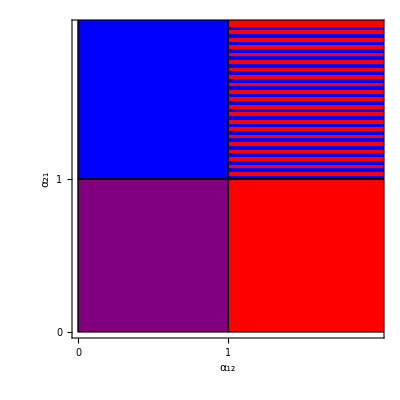

```mathematica
dx=1/41;op=1;coex=RegionPlot[{a12<1&&a21<1},{a12,0,2.1},{a21,0,2.1},PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
n1wins=RegionPlot[{a12<1&&a21>1},{a12,0,2.1},{a21,0,2.1},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
n2wins=RegionPlot[{a12>1&&a21<1},{a12,0,2.1},{a21,0,2.1},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
fc=RegionPlot[{a12>1&&a21>1},{a12,0,2.1},{a21,0,2.1},Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
Show[coex,n1wins,n2wins,fc,FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,1},None},{{0,1},None}},PlotRangePadding->0,PlotRange->{{0,2},{0,2}}]
```

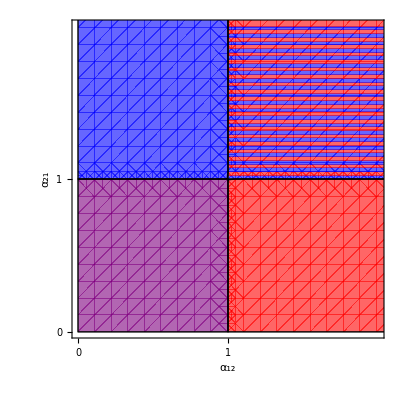

```mathematica
dx=1/41;op=0.6;coex=RegionPlot[{a12<1&&a21<1},{a12,0,2.1},{a21,0,2.1},PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
n1wins=RegionPlot[{a12<1&&a21>1},{a12,0,2.1},{a21,0,2.1},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
n2wins=RegionPlot[{a12>1&&a21<1},{a12,0,2.1},{a21,0,2.1},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
fc=RegionPlot[{a12>1&&a21>1},{a12,0,2.1},{a21,0,2.1},Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
Show[coex,n1wins,n2wins,fc,FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,1},None},{{0,1},None}},PlotRangePadding->0,PlotRange->{{0,2},{0,2}}]
```

```mathematica
r1=r2=1;
k1=50;k2=50;
m1=m2=0;
```

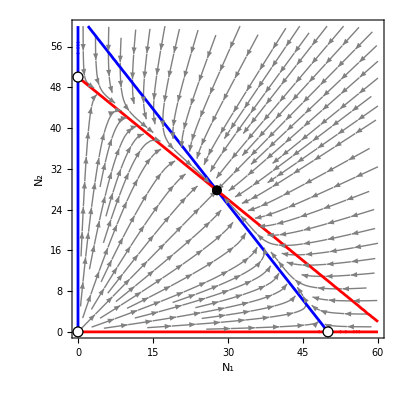

```mathematica
α12=0.8;α21=0.8;
eq=NSolveEcoEq[];
Show[
PlotEcoPhasePlane[{n1,0,60},{n2,0,60},FrameLabel->{Style["N_1",21],Style["N_2",21]},FrameStyle->Directive[18,Black]],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq],
StableMarker->{Graphics[{Black, Disk[{0, 0}]}, ImageSize -> 10, AlignmentPoint -> {0, 0}]},
UnstableMarker->{Graphics[{EdgeForm[{Black}],FaceForm[White],Disk[]},ImageSize->10,AlignmentPoint->{0,0}]}
]
]
```

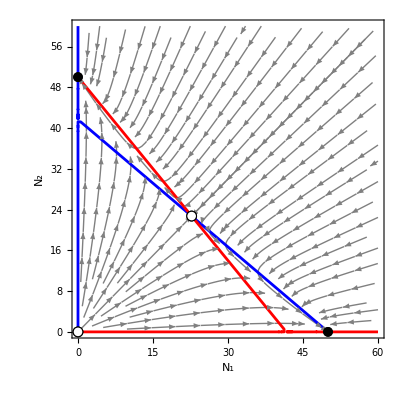

```mathematica
α12=1.2;α21=1.2;
eq=NSolveEcoEq[];
Show[
PlotEcoPhasePlane[{n1,0,60},{n2,0,60},PlotEcoIsoclinesOpts->{MaxRecursion->5},FrameLabel->{Style["N_1",21],Style["N_2",21]},FrameStyle->Directive[18,Black]],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq],
StableMarker->{Graphics[{Black, Disk[{0, 0}]}, ImageSize -> 10, AlignmentPoint -> {0, 0}]},
UnstableMarker->{Graphics[{EdgeForm[{Black}],FaceForm[White],Disk[]},ImageSize->10,AlignmentPoint->{0,0}]}
]
]
```

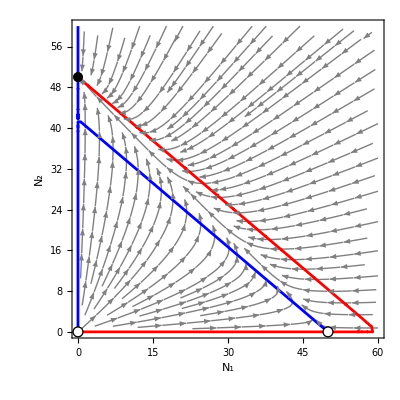

```mathematica
α12=1.2;α21=1/1.2;
eq=NSolveEcoEq[];
Show[
PlotEcoPhasePlane[{n1,0,60},{n2,0,60},PlotEcoIsoclinesOpts->{MaxRecursion->5},FrameLabel->{Style["N_1",21],Style["N_2",21]},FrameStyle->Directive[18,Black]],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq],
StableMarker->{Graphics[{Black, Disk[{0, 0}]}, ImageSize -> 10, AlignmentPoint -> {0, 0}]},
UnstableMarker->{Graphics[{EdgeForm[{Black}],FaceForm[White],Disk[]},ImageSize->10,AlignmentPoint->{0,0}]}
]
]
```

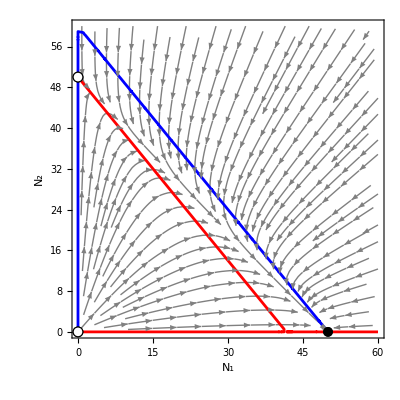

```mathematica
α12=1/1.2;α21=1.2;
eq=NSolveEcoEq[];
Show[
PlotEcoPhasePlane[{n1,0,60},{n2,0,60},PlotEcoIsoclinesOpts->{MaxRecursion->5},FrameLabel->{Style["N_1",21],Style["N_2",21]},FrameStyle->Directive[18,Black]],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq],
StableMarker->{Graphics[{Black, Disk[{0, 0}]}, ImageSize -> 10, AlignmentPoint -> {0, 0}]},
UnstableMarker->{Graphics[{EdgeForm[{Black}],FaceForm[White],Disk[]},ImageSize->10,AlignmentPoint->{0,0}]}
]
]
```

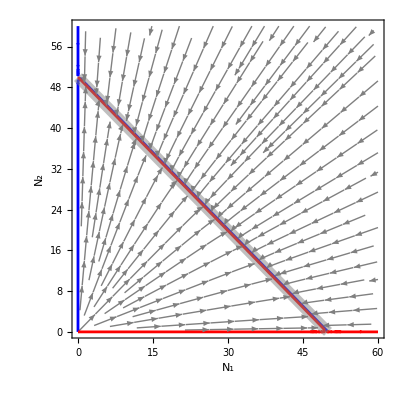

```mathematica
α12=1/1.005;α21=1.005;
Show[
PlotEcoPhasePlane[{n1,0,60},{n2,0,60},PlotEcoIsoclinesOpts->{MaxRecursion->5},FrameLabel->{Style["N_1",21],Style["N_2",21]},FrameStyle->Directive[18,Black]],
Plot[50-n1,{n1,0,50},PlotStyle->Directive[Thickness[0.02],Gray,Opacity[0.5]]]
]
```

```mathematica
SolveEcoEq[]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{n1→0,n2→0},{n2→50-n1}}

## Single Species

```mathematica
Clear[nr1,nr2]
```

```mathematica
r1=r2=1;
e=0;
k1=k2=50;
m1=m2=0.01;
Setnmax[2k1,2k2]
```

```mathematica
m1=0;nr1=0;
tmax=100;
sol=GillespieSSA[{
{{n1->n1+1},r1 n1+m1 nr1},(* birth/immigration 1 *)
{{n1->n1-1},(r1 n1^2/k1)+m1 n1}, (* death 1 *)
{{n1->0},e}(* extinction *)
},{n1->1},tmax];
```

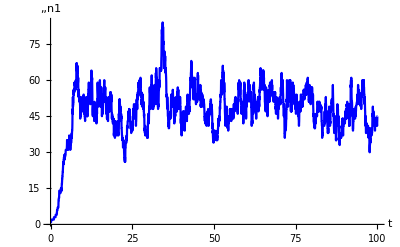

```mathematica
PlotDynamics[sol]
```

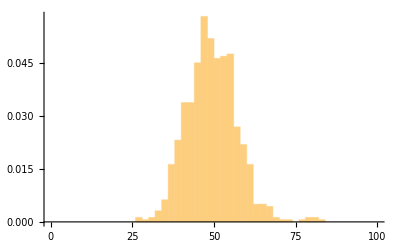

```mathematica
Histogram[Table[n1[t]/.sol,{t,20,100,0.1}],Automatic,"PDF",PlotRange->{{0,100},All}]
```

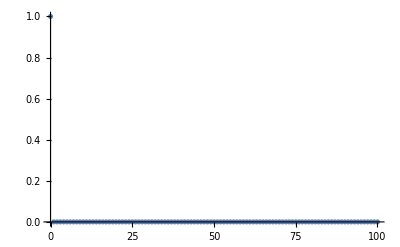

```mathematica
(* plot distribution *)
PlotDis1[GetDis1[0],Filling->Axis]
```

```mathematica
Clear[nr1];Eq1
PlotDis1[GetDis1[nr1/.Eq1],Filling->Axis]
```

{nr1→0.}

-Graphics-

{nr2→48.9789}

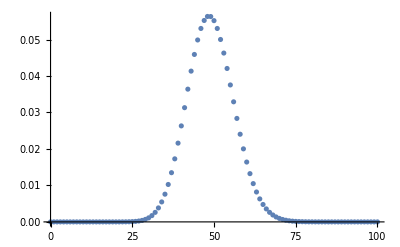

```mathematica
Eq2
PlotDis2[GetDis2[nr2/.Eq2]]
```

## Two Species Walkthrough

### Find equilibrium

```mathematica
Clear[nr1,nr2]
```

```mathematica
r1=r2=1;
e=0;
k1=50;
k2=50;
m1=m2=10^-2;
α12=0.9;α21=0.9;
Setnmax[2k1,2k2]
```

```mathematica
(* get distribution - fixed nr *)
dis=GetDis[{500,500}];
(* plot dis *)
PlotDis[dis,Nrs->{500,500}]
```

-Graphics3D-

```mathematica
(* find equilibrium *)
eq=Eq12
```

{nr1→25.1599,nr2→25.1599}

```mathematica
dis=GetDis[{nr1,nr2}/.eq];
PlotDis[dis,Nrs->{nr1,nr2}/.eq]
```

-Graphics3D-

```mathematica
ProbFrac[dis]
```

{-1→0,0.→0.255705,0.5→0.48859,1.→0.255705}

### Break probability into basins

```mathematica
op=1;
WatershedPlot[dis,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
(* prob by basin *)
Prob2[dis]//MatrixForm
```

(0 | 0.255705
0.255705 | 0.48859)

```mathematica
(* strict presence/absence *)
Prob2PA[dis]//MatrixForm
```

(8.0861×10^-21 | 0.106839
0.106839 | 0.786321)

```mathematica
(* 3-way decomposition *)
Prob3[dis]//MatrixForm
```

(0 | 0 | 0.106839
0 | 0 | 0.148866
0.106839 | 0.148866 | 0.48859)

### Simulate stochastic process

```mathematica
r1=r2=1;
e=0.01;
e=0;
k1=50;
k2=50;
m1=m2=10^-2;
α12=0.9;α21=0.9;
Setnmax[2k1,2k2]
```

```mathematica
eq
```

{nr1→25.1599,nr2→25.1599}

```mathematica
sol=StochSim[eq,{n1->(k1-k2 α12)/(1-α12 α21),n2->(k2-k1 α21)/(1-α12 α21)},1000];
```

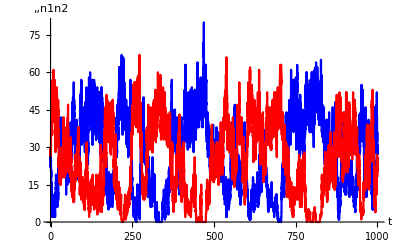

```mathematica
PlotDynamics[sol,PlotPoints->200,PlotRange->All]
```

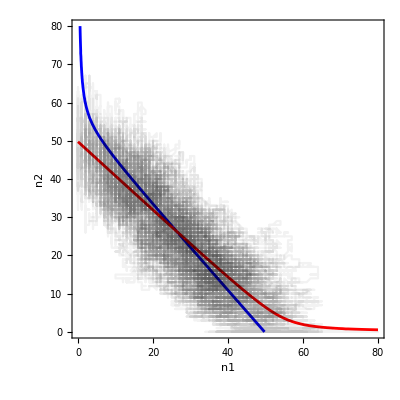

```mathematica
{nr1,nr2}={nr1,nr2}/.eq;
Show[
PlotEcoIsoclines[{n1,0,80},{n2,0,80}],
RuleListPlot[sol,PlotPoints->100000,PlotStyle->{{Black,Opacity[0.05]}},PlotRangePadding->1,PlotRange->{{0,80},{0,80}}]
]
Clear[nr1,nr2]
```

### Trying to make sense of how local founder control turns into regional exclusion, based on distances between equilibria

```mathematica
DeleteRowAndColumn[M_,x_]:=Transpose[Delete[Transpose[Delete[M,x]],x]];
```

```mathematica
r1=r2=1;
k1=k2=50;
e=0;
Setnmax[2k1,2k2]
```

```mathematica
λ12[α12in_?NumericQ,α21in_?NumericQ]:=Block[{α12,α21},{α12,α21}={α12in,α21in};Inv1[nr2/.Eq2]];
λ21[α12in_?NumericQ,α21in_?NumericQ]:=Block[{α12,α21},{α12,α21}={α12in,α21in};Inv2[nr1/.Eq1]];
```

#### (α12=1.8, α21=1.5) m=10^-1 — regional founder control

```mathematica
m1=m2=10^-1;
{α12,α21}={1.8,1.5};
```

```mathematica
{Eq1,Eq2}
```

{{nr1→48.9808},{nr2→48.9808}}

```mathematica
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{0.123783,0.209774}

Less::nord: Invalid comparison with -1.15412-0.248709 ⅈ attempted.

Greater::nord: Invalid comparison with -0.065179+0.223838 ⅈ attempted.

Greater::nord: Invalid comparison with -1.15412-0.248709 ⅈ attempted.

Less::nord: Invalid comparison with -0.065179+0.223838 ⅈ attempted.

Less::nord: Invalid comparison with -1.15412+0.248709 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -0.065179-0.223838 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

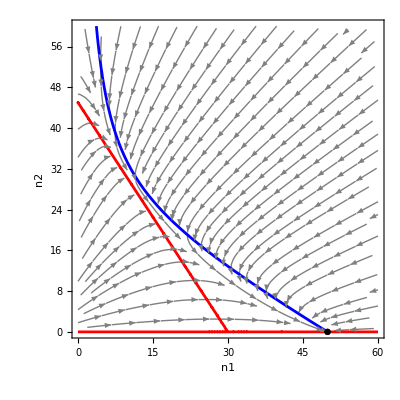

```mathematica
(* local phase plane with resident 1, invader 2 *)
Block[{nr1=(nr1/.Eq1),nr2=0,T},
Print[Show[
PlotEcoPhasePlane[{n1,0,1.2k1},{n2,0,1.2k2}],
RuleListPlot[eq=NSolveEcoEq[],PlotMarkers->EcoStableQ[eq]]
]];
(*T=Total[-Inverse[DeleteRowAndColumn[TM[i1,i2],k1+k2*(n1max+1)+1]]];
Print[T⟦0+k2*(n1max+1)+1⟧];
T=Total[-Inverse[DeleteRowAndColumn[TM[i1,i2],0+k2*(n1max+1)+1]]];
Print[T⟦k1+1⟧];*)
]
```

Less::nord: Invalid comparison with -1.01912+0.500669 ⅈ attempted.

Greater::nord: Invalid comparison with -0.245456-0.450603 ⅈ attempted.

Greater::nord: Invalid comparison with -1.01912+0.500669 ⅈ attempted.

Less::nord: Invalid comparison with -0.245456-0.450603 ⅈ attempted.

Less::nord: Invalid comparison with -1.01912-0.500669 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -0.245456+0.450603 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

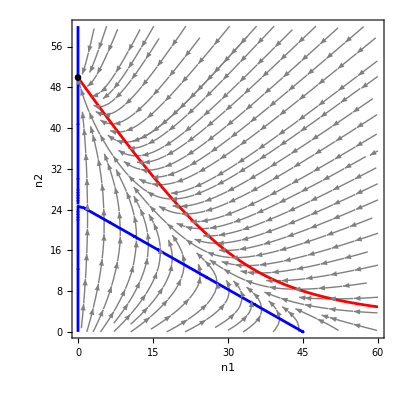

```mathematica
(* local phase plane with resident 2, invader 1 *)
Block[{nr1=0,nr2=(nr2/.Eq2)},
Show[
PlotEcoPhasePlane[{n1,0,1.2k1},{n2,0,1.2k2}],
RuleListPlot[eq=NSolveEcoEq[],PlotMarkers->EcoStableQ[eq]]
]
]
```

#### m=10^-1.46— barely 3 equilibria with resident 2

```mathematica
m1=m2=10^-1.46;
{α12,α21}={1.8,1.5};
```

```mathematica
{Eq1,Eq2}
```

{{nr1→48.9795},{nr2→48.9795}}

```mathematica
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{0.0478185,0.721507}

{{n1→49.9658,n2→0},{n1→20.2465,n2→17.8966},{n1→2.4671,n2→44.5657}}

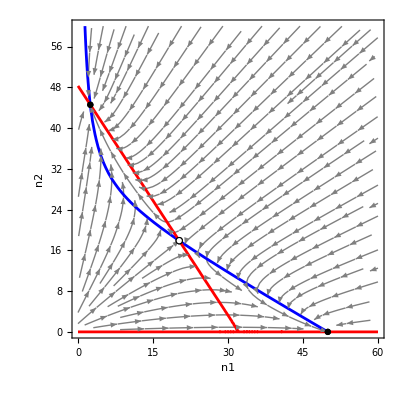

```mathematica
(* local phase plane with resident 1, invader 2 *)
Block[{nr1=(nr1/.Eq1),nr2=0},
eq=SelectValid@NSolveEcoEq[];
Print[eq];
Print[Show[
PlotEcoPhasePlane[{n1,0,1.2k1},{n2,0,1.2k2}],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]]
]
```

```mathematica
eq
```

{{n1→49.9658,n2→0},{n1→20.2465,n2→17.8966},{n1→2.4671,n2→44.5657}}

```mathematica
RuleListDistance[eq⟦1⟧,eq⟦2⟧]
RuleListDistance[eq⟦3⟧,eq⟦2⟧]
```

34.6919

32.0522

{{n1→0,n2→49.9658},{n1→36.6723,n2→6.44113},{n1→34.3076,n2→7.75484}}

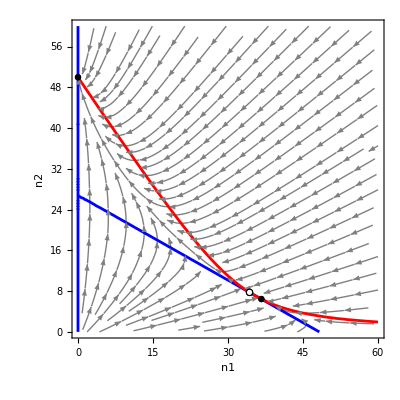

```mathematica
(* local phase plane with resident 2, invader 1 *)
Block[{nr1=0,nr2=(nr2/.Eq2)},
eq=SelectValid@NSolveEcoEq[];
Print[eq];
Show[
PlotEcoPhasePlane[{n1,0,1.2k1},{n2,0,1.2k2}],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]
]
```

```mathematica
RuleListDistance[eq⟦1⟧,eq⟦3⟧]
RuleListDistance[eq⟦2⟧,eq⟦3⟧]
```

54.3946

2.7051

#### m=10^-1.5— barely regional founder control (2 can almost invade 1)

```mathematica
m1=m2=10^-1.5;
{α12,α21}={1.8,1.5};
```

```mathematica
{Eq1,Eq2}
```

{{nr1→48.9794},{nr2→48.9794}}

```mathematica
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{0.0439416,0.963404}

{{n1→49.9687,n2→0},{n1→20.5708,n2→17.5626},{n1→2.21454,n2→45.0971}}

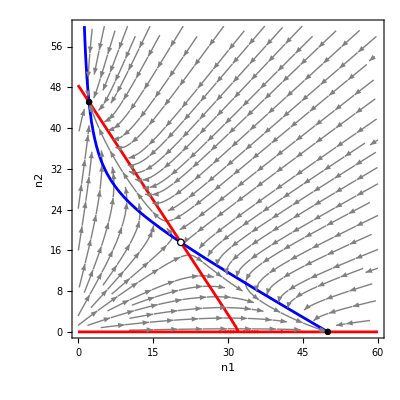

```mathematica
(* local phase plane with resident 1, invader 2 *)
Block[{nr1=(nr1/.Eq1),nr2=0},
eq=SelectValid@NSolveEcoEq[];
Print[eq];
Print[Show[
PlotEcoPhasePlane[{n1,0,1.2k1},{n2,0,1.2k2}],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]]
]
```

```mathematica
eq
```

{{n1→49.9687,n2→0},{n1→20.5708,n2→17.5626},{n1→2.21454,n2→45.0971}}

```mathematica
RuleListDistance[eq⟦1⟧,eq⟦2⟧]
RuleListDistance[eq⟦3⟧,eq⟦2⟧]
```

34.2445

33.0922

{{n1→0,n2→49.9687},{n1→31.519,n2→9.3888},{n1→39.6852,n2→4.85204}}

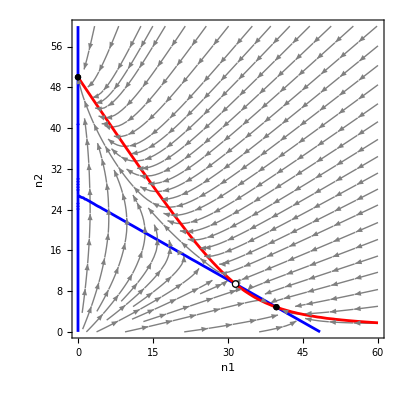

```mathematica
(* local phase plane with resident 2, invader 1 *)
Block[{i1=0,i2=im2/.Eq2},
eq=SelectValid@NSolveEcoEq[];
Print[eq];
Show[
PlotEcoPhasePlane[{n1,0,1.2k1},{n2,0,1.2k2}],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]
]
```

```mathematica
RuleListDistance[eq⟦1⟧,eq⟦3⟧]
RuleListDistance[eq⟦2⟧,eq⟦3⟧]
```

60.0868

9.34176

#### m=10^-1.51— 2 barely invades 1

```mathematica
m1=m2=10^-1.51;
{α12,α21}={1.8,1.5};
```

```mathematica
{Eq1,Eq2}
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{nr1→48.9794},{nr2→48.9794}}

```mathematica
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0430245,1.03537}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{n1→49.9694,n2→0},{n1→20.646,n2→17.4858},{n1→2.15624,n2→45.2205}}

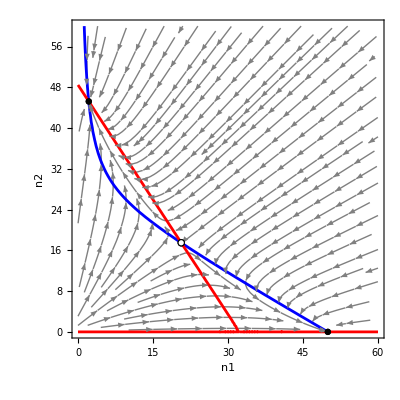

```mathematica
(* local phase plane with resident 1, invader 2 *)
Block[{nr1=(nr1/.Eq1),nr2=0},
eq=SelectValid@NSolveEcoEq[];
Print[eq];
Print[Show[
PlotEcoPhasePlane[{n1,0,1.2k1},{n2,0,1.2k2}],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]]
]
```

```mathematica
eq
```

{{n1→49.9694,n2→0},{n1→20.646,n2→17.4858},{n1→2.15624,n2→45.2205}}

```mathematica
RuleListDistance[eq⟦1⟧,eq⟦2⟧]
RuleListDistance[eq⟦3⟧,eq⟦2⟧]
```

34.1411

33.333

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{n1→0,n2→49.9694},{n1→40.1314,n2→4.62413},{n1→31.1257,n2→9.6273}}

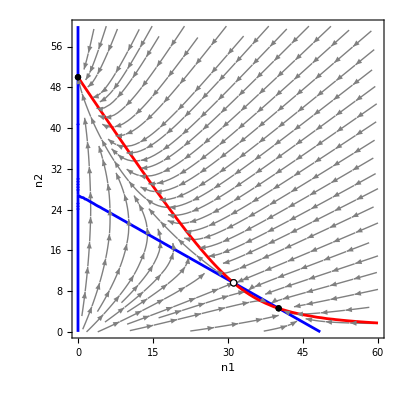

```mathematica
(* local phase plane with resident 2, invader 1 *)
Block[{nr1=0,nr2=(nr2/.Eq2)},
eq=SelectValid@NSolveEcoEq[];
Print[eq];
Show[
PlotEcoPhasePlane[{n1,0,1.2k1},{n2,0,1.2k2}],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]
]
```

```mathematica
RuleListDistance[eq⟦1⟧,eq⟦2⟧]
RuleListDistance[eq⟦3⟧,eq⟦2⟧]
```

60.5535

10.3021

#### m=10^-2 — 2 outcompetes 1

```mathematica
m1=m2=10^-2;
{α12,α21}={1.8,1.5};
```

```mathematica
{Eq1,Eq2}
```

{{nr1→48.9789},{nr2→48.9789}}

```mathematica
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{0.0174957,14.499}

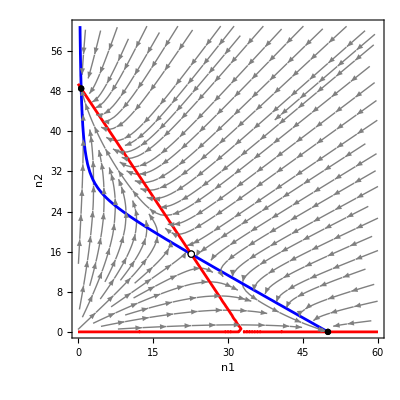

```mathematica
(* local phase plane with resident 1, invader 2 *)
Block[{nr1=(nr1/.Eq1),nr2=0},
eq=SelectValid@NSolveEcoEq[];
Print[Show[
PlotEcoPhasePlane[{n1,0,1.2k1},{n2,0,1.22k2}],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]];
(*T=Total[-Inverse[DeleteRowAndColumn[TM[i1,i2],k1+k2*(n1max+1)+1]]];
Print[T⟦0+k2*(n1max+1)+1⟧];
T=Total[-Inverse[DeleteRowAndColumn[TM[i1,i2],0+k2*(n1max+1)+1]]];
Print[T⟦k1+1⟧];*)
(*𝒫=ContinuousMarkovProcess[k1+1,Transpose@TM[i1,10^-5]];
Mean[FirstPassageTimeDistribution[𝒫,0+k2*(n1max+1)+1]]*)
]
```

```mathematica
eq
```

{{n1→49.9899,n2→0},{n1→22.6583,n2→15.5125},{n1→0.635773,n2→48.5463}}

```mathematica
RuleListDistance[eq⟦1⟧,eq⟦2⟧]
RuleListDistance[eq⟦3⟧,eq⟦2⟧]
```

31.4269

39.7018

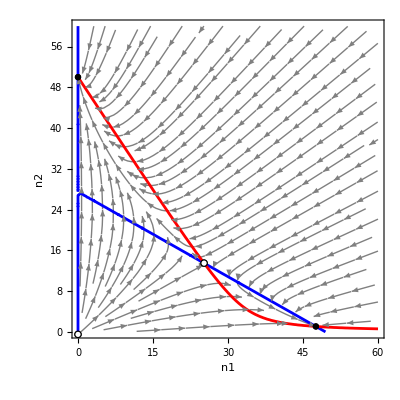

```mathematica
(* local phase plane with resident 2, invader 1 *)
Block[{nr1=0,nr2=(nr2/.Eq2)},
Show[
PlotEcoPhasePlane[{n1,0,1.2k1},{n2,0,1.2k2}],
RuleListPlot[eq=NSolveEcoEq[],PlotMarkers->EcoStableQ[eq]]
]
]
```

#### scan m, see how well distance between equilibria predicts invasion rate (close, not perfect)

```mathematica
Clear[m1,m2];
```

```mathematica
(* resident 1, invader 2 *)
res21=Table[
m1=m2=10^mp;
nr1=(nr1/.Eq1);nr2=0;
eq=SelectValid@NSolveEcoEq[];
{mp,Inv2[nr1/.Eq1],RuleListDistance[eq⟦1⟧,eq⟦2⟧],RuleListDistance[eq⟦3⟧,eq⟦2⟧]}
,{mp,-2,-1.1,0.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
(* resident 2, invader 1 *)
res12=Table[
m1=m2=10^mp;
nr1=0;nr2=(nr2/.Eq2);
eq=SelectValid@NSolveEcoEq[];
{mp,Inv1[nr2/.Eq2],RuleListDistance[eq⟦1⟧,eq⟦2⟧],RuleListDistance[eq⟦3⟧,eq⟦2⟧]}
,{mp,-2,-1.46,0.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

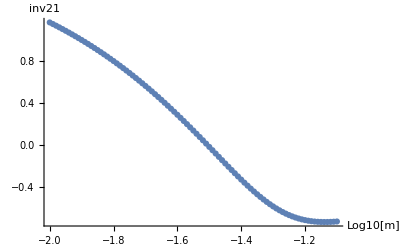

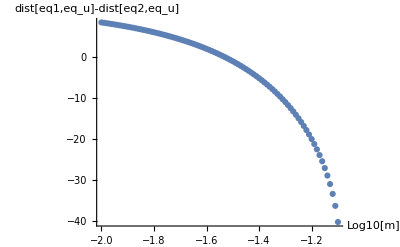

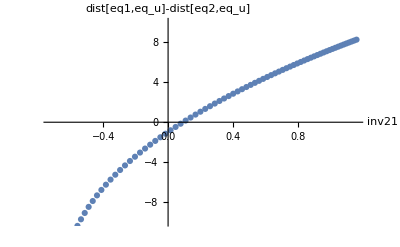

```mathematica
ListPlot[Transpose[{res21⟦All,1⟧,Log10[res21⟦All,2⟧]}],AxesLabel->{"Log10[m]","inv21"}]
ListPlot[Transpose[{res21⟦All,1⟧,res21⟦All,4⟧-res21⟦All,3⟧}],AxesLabel->{"Log10[m]","dist[eq1,eq_u]-dist[eq2,eq_u]"}]
ListPlot[Transpose[{Log10[res21⟦All,2⟧],res21⟦All,4⟧-res21⟦All,3⟧}],PlotRange->{-10,10},AxesLabel->{"inv21","dist[eq1,eq_u]-dist[eq2,eq_u]"}]
```

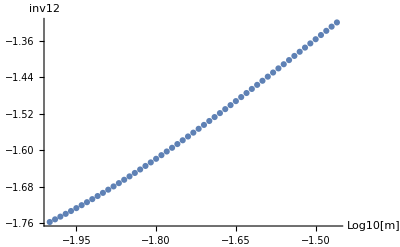

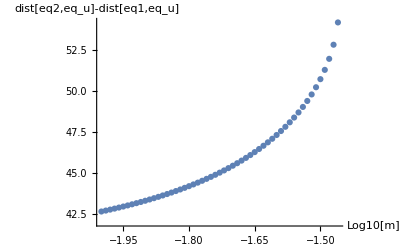

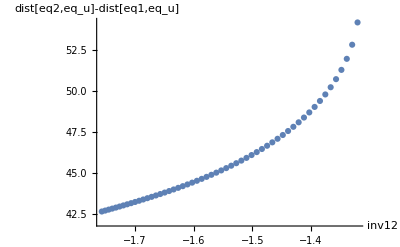

```mathematica
ListPlot[Transpose[{res12⟦All,1⟧,Log10[res12⟦All,2⟧]}],AxesLabel->{"Log10[m]","inv12"}]
ListPlot[Transpose[{res12⟦All,1⟧,res12⟦All,3⟧-res12⟦All,4⟧}],AxesLabel->{"Log10[m]","dist[eq2,eq_u]-dist[eq1,eq_u]"}]
ListPlot[Transpose[{Log10[res12⟦All,2⟧],res12⟦All,3⟧-res12⟦All,4⟧}],AxesLabel->{"inv12","dist[eq2,eq_u]-dist[eq1,eq_u]"}]
```

#### (α12=α21=1.1) m1=0.001, m2=0.002 — 2 wins

```mathematica
Clear[nr1,nr2]
```

```mathematica
α12=α21=1.1;
{m1,m2}={0.001,0.002};
```

```mathematica
{Eq1,Eq2}
```

{{nr1→48.9787},{nr2→48.9787}}

```mathematica
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{0.452026,1.76426}

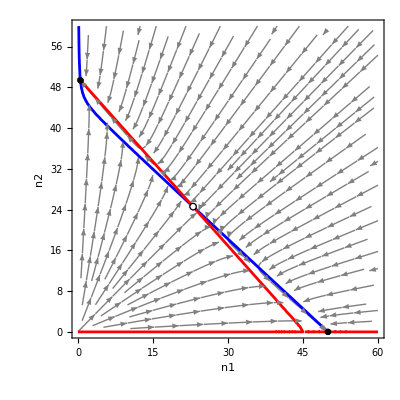

{{n1→49.999,n2→0},{n1→23.0172,n2→24.5811},{n1→0.506648,n2→49.3427}}

d(1,saddle)=36.5

d(2,saddle)=33.4643

```mathematica
(* local phase plane with resident 1, invader 2 *)
Block[{nr1=(nr1/.Eq1),nr2=0},
eq=SelectValid@NSolveEcoEq[];
Print[Show[
PlotEcoPhasePlane[{n1,0,1.2k1},{n2,0,1.2k2}],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]];
]
eq
Print["d(1,saddle)=",RuleListDistance[eq⟦1⟧,eq⟦2⟧]];
Print["d(2,saddle)=",RuleListDistance[eq⟦3⟧,eq⟦2⟧]];
```

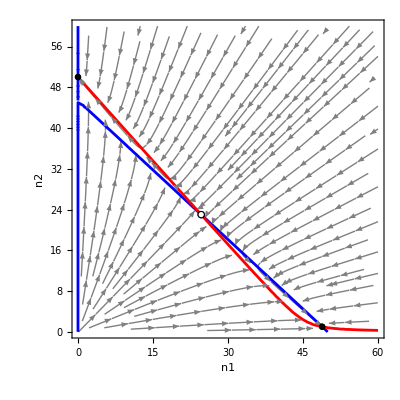

{{n1→0,n2→49.998},{n1→48.835,n2→1.0136},{n1→24.6388,n2→23.0102}}

d(1,saddle)=36.5432

d(2,saddle)=32.7003

```mathematica
(* local phase plane with resident 2, invader 1 *)
Block[{nr1=0,nr2=(nr2/.Eq2)},
eq=SelectValid@NSolveEcoEq[];
Show[
PlotEcoPhasePlane[{n1,0,1.2k1},{n2,0,1.2k2}],
RuleListPlot[eq,PlotMarkers->EcoStableQ[eq]]
]
]
eq
Print["d(1,saddle)=",RuleListDistance[eq⟦1⟧,eq⟦3⟧]];
Print["d(2,saddle)=",RuleListDistance[eq⟦2⟧,eq⟦3⟧]];
```

## Open System

```mathematica
Clear[nr1,nr2]
```

### Fig 2 — 1 wins (α12=1.25, α21=0.8)

#### A-B) m1=m2=10^-3

```mathematica
r1=r2=1;
e=0;
k1=50;
k2=50;
Setnmax[2k1,2k2];

{α12,α21}={1.25,0.8};
{m1,m2}={10^-3,10^-3};
dis=GetDis[{k1,k2}];

PlotDis[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
WatershedPlot[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
SquarePie[dis]
```

-Graphics-

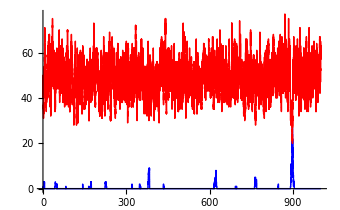

```mathematica
sol=StochSim[{nr1->k1,nr2->k2},{n1->0,n2->k2},1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

#### C-D) m1=m2=10^-2

```mathematica
r1=r2=1;
e=0;
k1=50;
k2=50;
Setnmax[2k1,2k2];

{α12,α21}={1.25,0.8};
{m1,m2}={10^-2,10^-2};
dis=GetDis[{k1,k2}];

PlotDis[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
WatershedPlot[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
SquarePie[dis]
```

-Graphics-

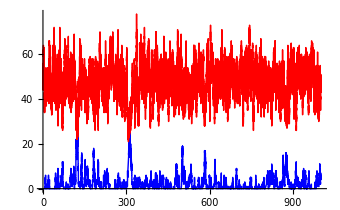

```mathematica
sol=StochSim[{nr1->k1,nr2->k2},{n1->0,n2->k2},1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

#### E-F) m1=m2=10^-1

```mathematica
r1=r2=1;
e=0;
k1=50;
k2=50;
Setnmax[2k1,2k2];

{α12,α21}={1.25,0.8};
{m1,m2}={10^-1,10^-1};
dis=GetDis[{k1,k2}];

PlotDis[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
WatershedPlot[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
SquarePie[dis]
```

-Graphics-

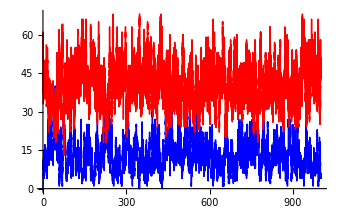

```mathematica
SeedRandom[7];
sol=StochSim[{nr1->k1,nr2->k2},{n1->0,n2->k2},1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

### Fig 3 — coexistence (α12=α21=0.9)

#### A-B) m1=m2=10^-3

```mathematica
r1=r2=1;
e=0;
k1=50;
k2=50;
Setnmax[2k1,2k2];

{α12,α21}={0.9,0.9};
{m1,m2}={10^-3,10^-3};
dis=GetDis[{k1,k2}];

PlotDis[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
WatershedPlot[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
SquarePie[dis]
```

-Graphics-

```mathematica
WatershedPlot[dis,ImageSize->400,PlotRange->{10^-5,All}]
```

-Graphics3D-

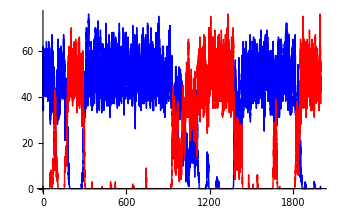

```mathematica
SeedRandom[7];
sol=StochSim[{nr1->k1,nr2->k2},eq[[2]],2000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

#### C-D) m1=m2=10^-2

```mathematica
r1=r2=1;
e=0;
k1=50;
k2=50;
Setnmax[2k1,2k2];

{α12,α21}={0.9,0.9};
{m1,m2}={10^-2,10^-2};
dis=GetDis[{k1,k2}];

PlotDis[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
WatershedPlot[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
SquarePie[dis]
```

-Graphics-

```mathematica
WatershedPlot[dis,ImageSize->400,PlotRange->{10^-5,All}]
```

-Graphics3D-

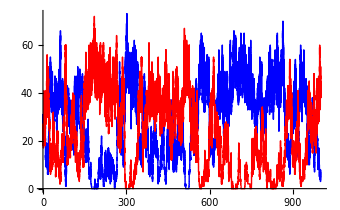

```mathematica
SeedRandom[7];
sol=StochSim[{nr1->k1,nr2->k2},eq[[-1]],1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

#### E-F) m1=m2=10^-1

```mathematica
r1=r2=1;
e=0;
k1=50;
k2=50;
Setnmax[2k1,2k2];

{α12,α21}={0.9,0.9};
{m1,m2}={10^-1,10^-1};
dis=GetDis[{k1,k2}];

PlotDis[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
WatershedPlot[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
SquarePie[dis]
```

-Graphics-

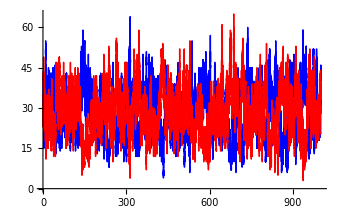

```mathematica
sol=StochSim[{nr1->k1,nr2->k2},eq[[-1]],1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

### Fig 4 — founder control (α12=1.2, α21=1.2)

#### A-B) m1=m2=10^-3

```mathematica
r1=r2=1;
e=0;
k1=50;
k2=50;
Setnmax[2k1,2k2];

{α12,α21}={1.2,1.2};
{m1,m2}={10^-3,10^-3};
dis=GetDis[{k1,k2}];

PlotDis[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
WatershedPlot[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
SquarePie[dis]
```

-Graphics-

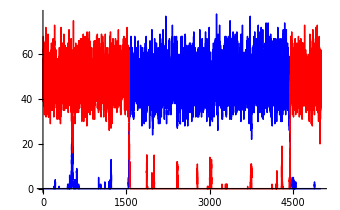

```mathematica
SeedRandom[3];
sol=StochSim[{nr1->k1,nr2->k2},{n1->0,n2->k2},5000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

#### C-D) m1=m2=10^-1.5

```mathematica
r1=r2=1;
e=0;
k1=50;
k2=50;
Setnmax[2k1,2k2];

{α12,α21}={1.2,1.2};
{m1,m2}={10^-1.5,10^-1.5};
dis=GetDis[{k1,k2}];

PlotDis[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
WatershedPlot[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
SquarePie[dis]
```

-Graphics-

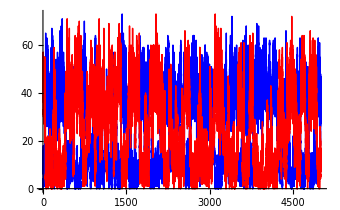

```mathematica
SeedRandom[3];
sol=StochSim[{nr1->k1,nr2->k2},{n1->0,n2->k2},5000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

#### E-F) m1=m2=10^-1

```mathematica
r1=r2=1;
e=0;
k1=50;
k2=50;
Setnmax[2k1,2k2];

{α12,α21}={1.2,1.2};
{m1,m2}={10^-1,10^-1};
dis=GetDis[{k1,k2}];

PlotDis[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
WatershedPlot[dis,ImageSize->400]
```

-Graphics3D-

```mathematica
SquarePie[dis]
```

-Graphics-

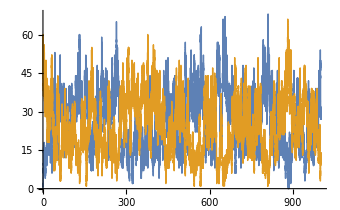

```mathematica
SeedRandom[3];
sol=StochSim[{nr1->k1,nr2->k2},{n1->0,n2->k2},1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

### Fig S1 — α scan, various k

```mathematica
r1=r2=1;
e=0;
m1=m2=10^-3;
```

```mathematica
k1=50;
k2=50;
Setnmax[2k1,2k2];

dα=0.1;
Rasterize[Show[Graphics[Flatten[Table[
    Inset[SquarePie[GetDis[{k1,k2}]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
k1=100;
k2=100;
Setnmax[2k1,2k2];

dα=0.1;
Rasterize[Show[Graphics[Flatten[Table[
    Inset[SquarePie[GetDis[{k1,k2}]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
k1=200;
k2=200;
Setnmax[2k1,2k2];

dα=0.1;
Rasterize[Show[Graphics[Flatten[Table[
    Inset[SquarePie[GetDis[{k1,k2}]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

### Fig 5 — α scan, various m

```mathematica
r1=r2=1;
e=0;
k1=50;
k2=50;
Setnmax[2k1,2k2];
```

```mathematica
m1=m2=10^-1;
dα=0.1;
Rasterize[Show[Graphics[Flatten[Table[
    Inset[SquarePie[GetDis[{k1,k2}]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
m1=m2=10^-1.5;
dα=0.1;
Rasterize[Show[Graphics[Flatten[Table[
    Inset[SquarePie[GetDis[{k1,k2}]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
m1=m2=10^-2;
dα=0.1;
Rasterize[Show[Graphics[Flatten[Table[
    Inset[SquarePie[GetDis[{k1,k2}]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
m1=m2=10^-3;
dα=0.1;
Rasterize[Show[Graphics[Flatten[Table[
    Inset[SquarePie[GetDis[{k1,k2}]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
m1=m2=10^-5;
dα=0.1;
Rasterize[Show[Graphics[Flatten[Table[
    Inset[SquarePie[GetDis[{n1r,n2r}]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
BarLegend[{cf,{0.001,0.999}},LabelStyle->Directive[Black, 16],Method->{TicksStyle->{Black,Thickness[0.004]},FrameStyle->Directive[Thickness[0.005],Black]},LegendLayout->"Row"]
Graphics[{EdgeForm[Thickness[0.08]],Red,Rectangle[]},ImageSize->20]
Graphics[{EdgeForm[Thickness[0.08]],Blue,Rectangle[]},ImageSize->20]
```

-Graphics-

-Graphics-

### probf plots

```mathematica
r1=r2=1;
e=0;
k1=50;
k2=50;
Setnmax[2k1,2k2]
```

```mathematica
Dynamic[{α,f}]
```

```mathematica
Clear[α12,α21];
{n1r,n2r}={k1/2,k2/2};
m1=m2=10^-1;
res01=Flatten[Table[
α12=α21=α;
dis=GetDis[{m1 n1r,m2 n2r}];
Table[{α,f,Probf[dis,f]},{f,0.01,0.99,0.02}]
,{α,0,2,0.02}],1];
```

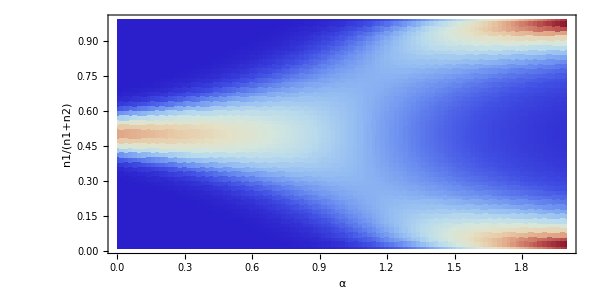

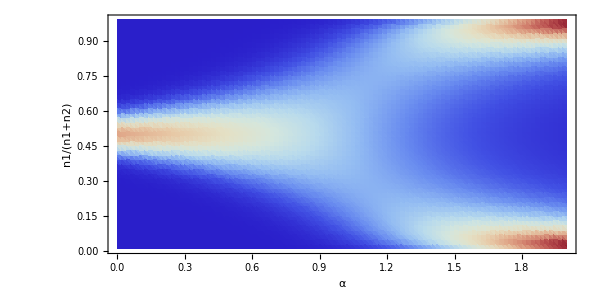

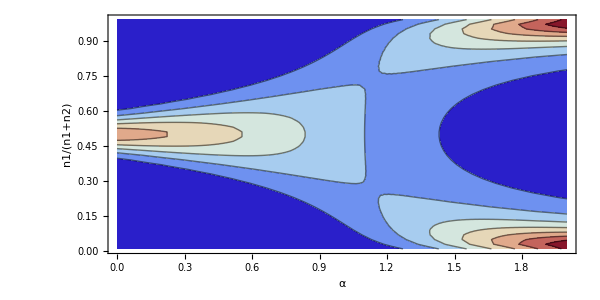

-Graphics3D-

```mathematica
ListDensityPlot[res01,AspectRatio->1/2,ImageSize->600,ColorFunction->"ThermometerColors",FrameLabel->{α,n1/(n1+n2)},InterpolationOrder->0]
ListDensityPlot[res01,AspectRatio->1/2,ImageSize->600,ColorFunction->"ThermometerColors",FrameLabel->{α,n1/(n1+n2)}]
ListContourPlot[res01,AspectRatio->1/2,ImageSize->600,ColorFunction->"ThermometerColors",FrameLabel->{α,n1/(n1+n2)}]
ListPlot3D[res01,AspectRatio->1/2,ImageSize->600,ColorFunction->"ThermometerColors",AxesLabel->{α,n1/(n1+n2),p}]
```

```mathematica
Clear[α12,α21];
{n1r,n2r}={k1/2,k2/2};
m1=m2=10^-2;
res001=Flatten[Table[
α12=α21=α;
dis=GetDis[{m1 n1r,m2 n2r}];
Table[{α,f,Probf[dis,f]},{f,0.01,0.99,0.02}]
,{α,0,2,0.02}],1];
```

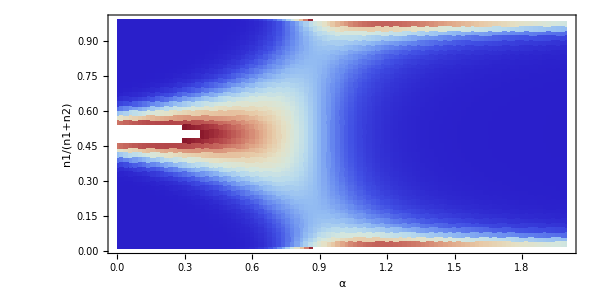

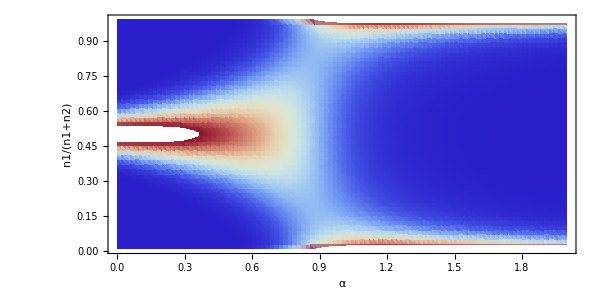

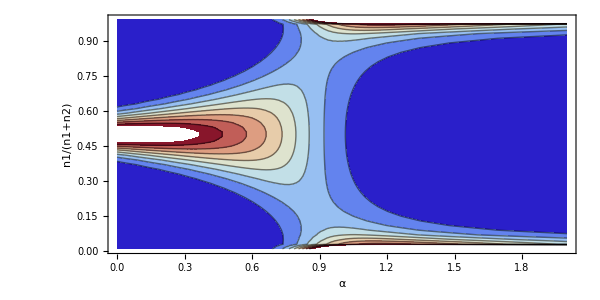

-Graphics3D-

```mathematica
ListDensityPlot[res001,AspectRatio->1/2,ImageSize->600,ColorFunction->"ThermometerColors",FrameLabel->{α,n1/(n1+n2)},InterpolationOrder->0]
ListDensityPlot[res001,AspectRatio->1/2,ImageSize->600,ColorFunction->"ThermometerColors",FrameLabel->{α,n1/(n1+n2)}]
ListContourPlot[res001,AspectRatio->1/2,ImageSize->600,ColorFunction->"ThermometerColors",FrameLabel->{α,n1/(n1+n2)}]
ListPlot3D[res001,AspectRatio->1/2,ImageSize->600,ColorFunction->"ThermometerColors",AxesLabel->{α,n1/(n1+n2),p}]
```

## Metacommunity Model

### Fig 6 — α12-α21, equal m

```mathematica
Clear[nr1,nr2,α12,α21];
r1=r2=1;
k1=k2=50;
e=0;
Setnmax[2k1,2k2]
```

```mathematica
λ12[α12in_?NumericQ,α21in_?NumericQ]:=λ12[α12in,α21in]=Block[{α12=α12in,α21=α21in},Inv1[nr2/.Eq2]];
λ21[α12in_?NumericQ,α21in_?NumericQ]:=λ21[α12in,α21in]=Block[{α12=α12in,α21=α21in},Inv2[nr1/.Eq1]];
```

```mathematica
dx=1/41;
```

#### m=10^0

```mathematica
m1=m2=10^0;
```

```mathematica
ClearCache[λ12,λ21]
```

```mathematica
op=1;
```

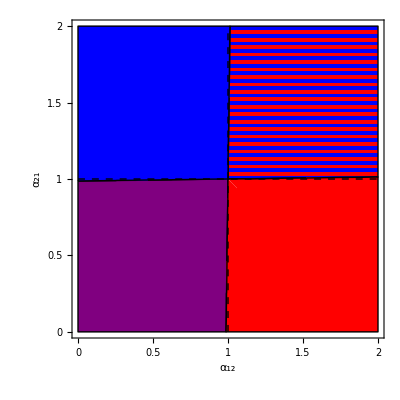

```mathematica
fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0]
```

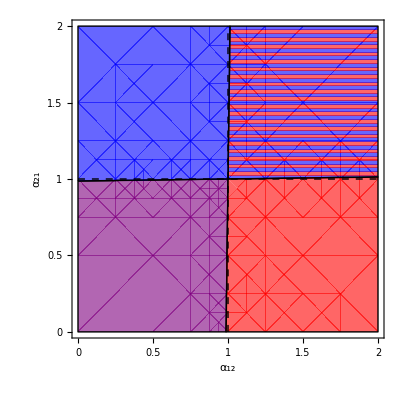

```mathematica
op=0.6;fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0]
```

#### m=10^-1

```mathematica
m1=m2=10^-1;
```

```mathematica
ClearCache[λ12,λ21]
```

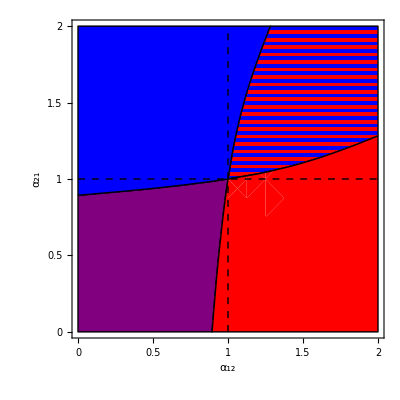

```mathematica
(* 129 s *)
op=1;
fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0(*,PlotRange->{{0,2},{0,2}}*)(*,Frame->{True,True,False,False}*)]
```

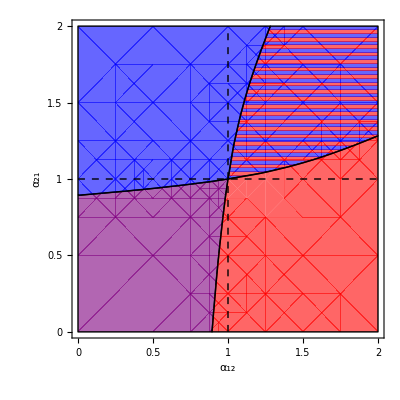

```mathematica
(* 129 s *)
op=0.6;
fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0(*,PlotRange->{{0,2},{0,2}}*)(*,Frame->{True,True,False,False}*)]
```

```mathematica
Clear[α12,α21];
Dynamic[{α12,α21}]
Do[
dis=GetDis[{im1,im2}/.Eq12];
pd[α12,α21]=Prob2[dis]
,{α12,0.0,1.0,0.02},{α21,0.0,1.0,0.02}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Rasterize[Show[Table[SquarePie[pd[α12,α21],{{α12-0.0098,α21-0.0098},{α12+0.0098,α21+0.0098}}],{α12,0.0,1.0,0.02},{α21,0.0,1.0,0.02}],PlotRange->{{-0.01,1.01},{-0.01,1.01}},ImageSize->Large],ImageResolution->300]
```

-Graphics-

#### m=10^-2

```mathematica
m1=m2=10^-2;
```

```mathematica
ClearCache[λ12,λ21]
```

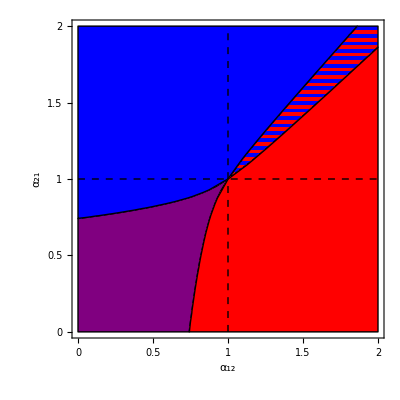

```mathematica
(* 170.3 s *)
op=1;fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0(*,PlotRange->{{0,2},{0,2}}*)(*,Frame->{True,True,False,False}*)]
```

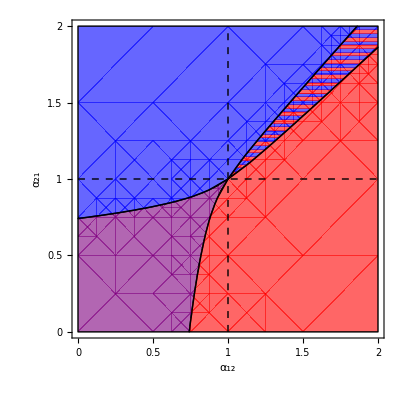

```mathematica
op=0.6;fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0(*,PlotRange->{{0,2},{0,2}}*)(*,Frame->{True,True,False,False}*)]
```

```mathematica
Clear[α12,α21];
Dynamic[{α12,α21}]
Do[
dis=GetDis[{im1,im2}/.Eq12];
pd[α12,α21]=Prob2[dis]
,{α12,0.0,1.0,0.02},{α21,0.0,1.0,0.02}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Rasterize[Show[Table[SquarePie[pd[α12,α21],{{α12-0.0098,α21-0.0098},{α12+0.0098,α21+0.0098}}],{α12,0.0,1.0,0.02},{α21,0.0,1.0,0.02}],PlotRange->{{-0.01,1.01},{-0.01,1.01}},ImageSize->Large],ImageResolution->300]
```

-Graphics-

```mathematica
Rasterize[Show[Table[SquarePie[pd[α12,α21],{{α21-0.0098,α12-0.0098},{α21+0.0098,α12+0.0098}}],{α12,0.0,1.0,0.02},{α21,0.0,1.0,0.02}],PlotRange->{{-0.01,1.01},{-0.01,1.01}},ImageSize->Large],ImageResolution->300]
```

-Graphics-

#### m=10^-3

```mathematica
m1=m2=10^-3;
```

```mathematica
ClearCache[λ12,λ21]
```

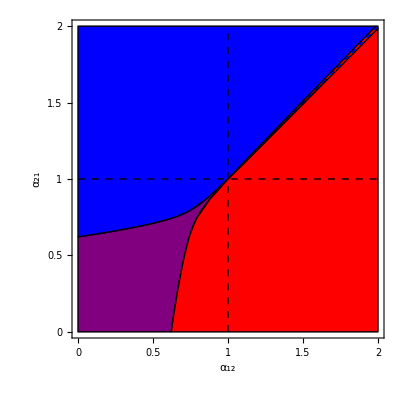

```mathematica
(* 145 s *)
op=1;
fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0]
```

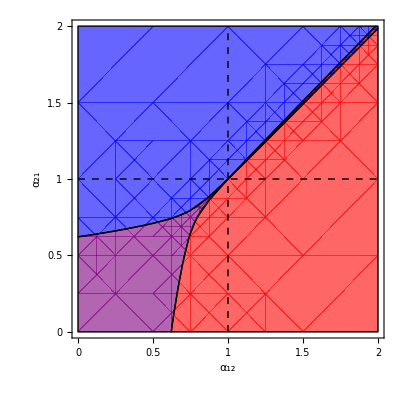

```mathematica
op=0.6;
fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0]
```

```mathematica
Clear[α12,α21];
Dynamic[{α12,α21}]
Do[
dis=GetDis[{im1,im2}/.Eq12];
pd[α12,α21]=Prob2[dis]
,{α12,0.0,1.0,0.02},{α21,0.0,1.0,0.02}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
Rasterize[Show[Table[SquarePie[pd[α12,α21],{{α12-0.0098,α21-0.0098},{α12+0.0098,α21+0.0098}}],{α12,0.0,1.0,0.02},{α21,0.0,1.0,0.02}],PlotRange->{{-0.01,1.01},{-0.01,1.01}},ImageSize->Large],ImageResolution->300]
```

-Graphics-

#### m=10^-4

```mathematica
m1=m2=10^-4;
```

```mathematica
ClearCache[λ12,λ21]
```

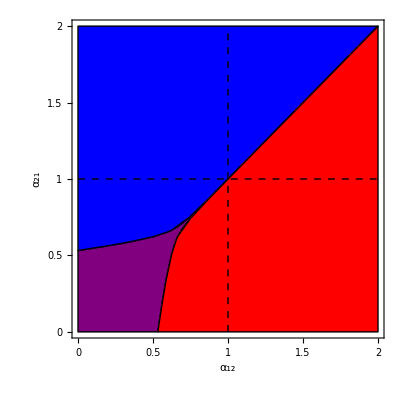

```mathematica
(* 152 s *)
op=1;
fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0]
```

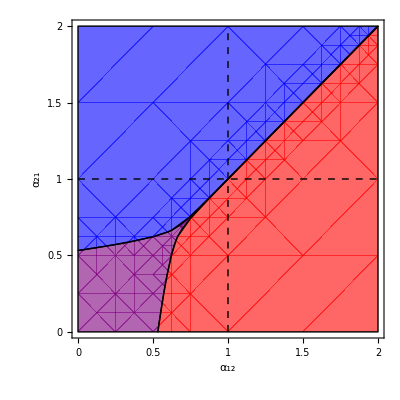

```mathematica
op=0.6;
fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0]
```

```mathematica
Clear[α12,α21];
Dynamic[{α12,α21}]
Do[
dis=GetDis[{im1,im2}/.Eq12];
pd[α12,α21]=Prob2[dis]
,{α12,0.0,1.0,0.02},{α21,0.0,1.0,0.02}]
```

```mathematica
Rasterize[Show[Table[SquarePie[pd[α12,α21],{{α12-0.0098,α21-0.0098},{α12+0.0098,α21+0.0098}}],{α12,0.0,1.0,0.02},{α21,0.0,1.0,0.02}],PlotRange->{{-0.01,1.01},{-0.01,1.01}},ImageSize->Large],ImageResolution->300]
```

-Graphics-

#### m=10^-5

```mathematica
m1=m2=10^-5;
```

```mathematica
ClearCache[λ12,λ21]
```

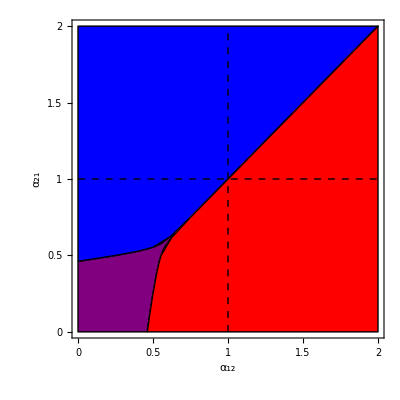

```mathematica
(* 183 s *)
op=1;
fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0]
```

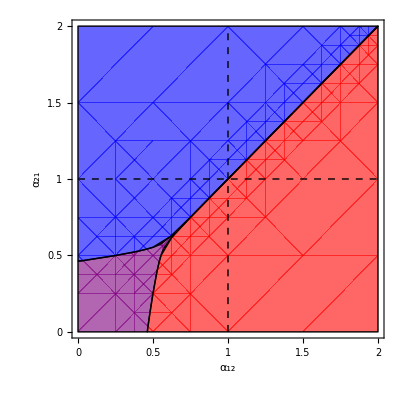

```mathematica
op=0.6;
fc=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,Mesh->{Table[x,{x,0,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
inv1=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]<1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
inv2=RegionPlot[λ12[α12in,α21in]<1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[α12in,α21in]>1&&λ21[α12in,α21in]>1,{α12in,0,2},{α21in,0,2},PlotPoints->5,MaxRecursion->3,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
Show[coex,fc,inv1,inv2,
Graphics[{{Dashed,Black,Line[{{1,0},{1,2}}]},{Dashed,Black,Line[{{0,1},{2,1}}]}}],FrameStyle->Directive[18,Black],FrameLabel->{Style["α_12",21],Style["α_21",21]},
FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},PlotRangePadding->0]
```

```mathematica
Clear[α12,α21];
Dynamic[{α12,α21}]
Do[
dis=GetDis[{im1,im2}/.Eq12];
pd[α12,α21]=Prob2[dis]
,{α12,0.0,1.0,0.02},{α21,0.0,1.0,0.02}]
```

```mathematica
Rasterize[Show[Table[SquarePie[pd[α12,α21],{{α12-0.0098,α21-0.0098},{α12+0.0098,α21+0.0098}}],{α12,0.0,1.0,0.02},{α21,0.0,1.0,0.02}],PlotRange->{{-0.01,1.01},{-0.01,1.01}},ImageSize->Large],ImageResolution->300]
```

-Graphics-

### Fig S2 — squarepies in coex region

```mathematica
Clear[nr1,nr2,α12,α21];
r1=r2=1;
k1=k2=50;
e=0;
Setnmax[2k1,2k2]
```

```mathematica
λ12[α12in_?NumericQ,α21in_?NumericQ]:=λ12[α12in,α21in]=Block[{α12=α12in,α21=α21in},Inv1[nr2/.Eq2]];
λ21[α12in_?NumericQ,α21in_?NumericQ]:=λ21[α12in,α21in]=Block[{α12=α12in,α21=α21in},Inv2[nr1/.Eq1]];
```

```mathematica
m1=m2=10^-2;
```

```mathematica
ClearCache[λ12,λ21]
```

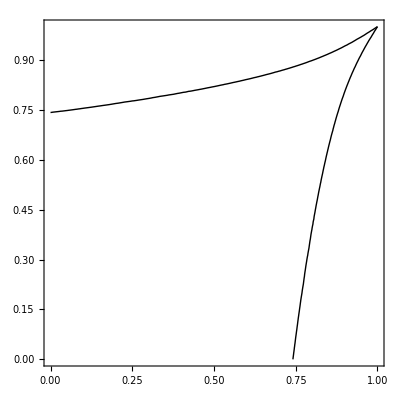

```mathematica
coexplot=ContourPlot[{λ12[α12in,α21in]==1,λ21[α12in,α21in]==1},{α12in,0,1},{α21in,0,1},PlotPoints->5,MaxRecursion->3,ContourStyle->Directive[Thick,Black],Background->Opacity[0]]
```

```mathematica
Dynamic[{α12,α21}]
```

```mathematica
Clear[α12,α21];
dα=0.02;
pies=Graphics[Flatten[Table[
    Inset[SquarePie[GetDis[{nr1,nr2}/.Eq12]],{α12,α21},{0,0},0.99dα]
   ,{α12,0.0,1.0,dα},{α21,0.0,1.0,dα}],1]
  ];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Rasterize[Show[pies,coexplot,Frame->True,PlotRange->{{-0.02-dα/2,1.02+dα/2},{-0.02-dα/2,1.02+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->Automatic,FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

```mathematica
m1=m2=10^-5;
```

```mathematica
ClearCache[λ12,λ21]
```

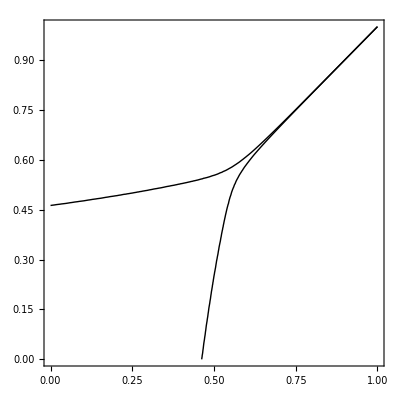

```mathematica
coexplot=ContourPlot[{λ12[α12in,α21in]==1,λ21[α12in,α21in]==1},{α12in,0,1},{α21in,0,1},PlotPoints->5,MaxRecursion->3,ContourStyle->Directive[Thick,Black],Background->Opacity[0]]
```

```mathematica
Dynamic[{α12,α21}]
```

```mathematica
Clear[α12,α21];
dα=0.02;
pies=Graphics[Flatten[Table[
    Inset[SquarePie[GetDis[{nr1,nr2}/.Eq12]],{α12,α21},{0,0},0.99dα]
   ,{α12,0.0,1.0,dα},{α21,0.0,1.0,dα}],1]
  ];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Rasterize[Show[pies,coexplot,Frame->True,PlotRange->{{-0.02-dα/2,1.02+dα/2},{-0.02-dα/2,1.02+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->Automatic,FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

### Fig 7 — m1-m2, equal α, e=0

```mathematica
r1=r2=1;
k1=k2=50;
e=0;
Setnmax[2k1,2k2]
```

```mathematica
Clear[m1,m2]
```

```mathematica
λ12[m1in_?NumericQ,m2in_?NumericQ]:=λ12[m1in,m2in]=({m1,m2}={m1in,m2in};Inv1[nr2/.Eq2]);
λ21[m1in_?NumericQ,m2in_?NumericQ]:=λ21[m1in,m2in]=({m1,m2}={m1in,m2in};Inv2[nr1/.Eq1]);
```

```mathematica
dx=3/41;
```

#### a) α12=α21=0.9

```mathematica
α12=α21=0.9;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
op=1;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 312 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 116.5s *)
coex=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

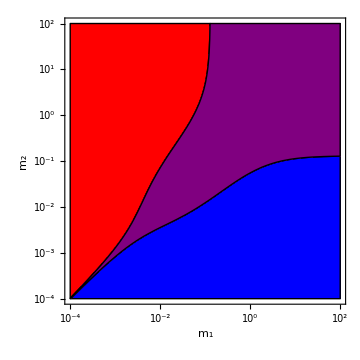

```mathematica
Show[n1wins,n2wins,coex,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

```mathematica
op=0.6;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 287 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 116.5s *)
coex=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

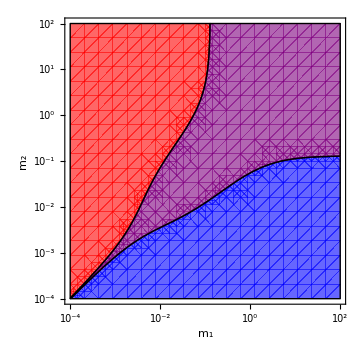

```mathematica
Show[n1wins,n2wins,coex,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

#### b) α12=α21=0.99

```mathematica
α12=α21=0.99;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
op=1;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 312 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 116.5s *)
coex=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

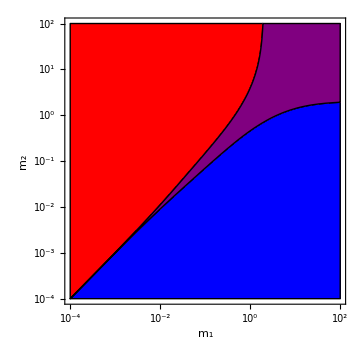

```mathematica
Show[n1wins,n2wins,coex,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

```mathematica
op=0.6;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 287 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 116.5s *)
coex=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

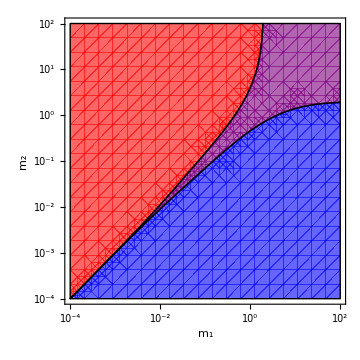

```mathematica
Show[n1wins,n2wins,coex,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

#### c) α12=α21=1

```mathematica
α12=α21=1;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
op=1;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 312 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

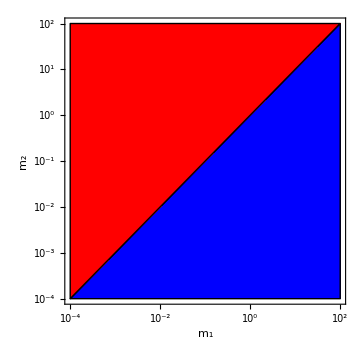

```mathematica
Show[n1wins,n2wins,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

```mathematica
op=0.6;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 287 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

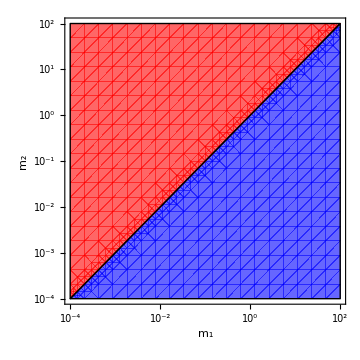

```mathematica
Show[n1wins,n2wins,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

#### d) α12=α21=1.01

```mathematica
α12=α21=1.01;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
op=1;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 312 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* X s *)
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

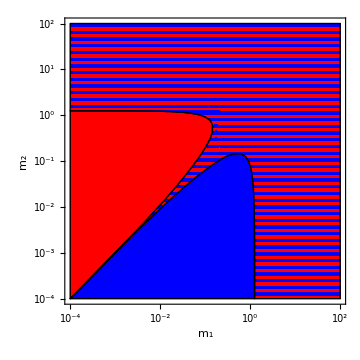

```mathematica
Show[n1wins,n2wins,fc,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

```mathematica
op=0.6;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 287 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* X s *)
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

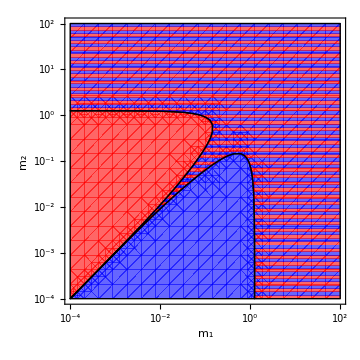

```mathematica
Show[n1wins,n2wins,fc,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

#### e) α12=α21=1.1

```mathematica
α12=α21=1.1;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
op=1;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 312 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* X s *)
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

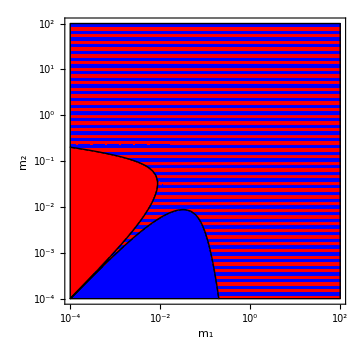

```mathematica
Show[n1wins,n2wins,fc,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

```mathematica
op=0.6;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 287 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* X s *)
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

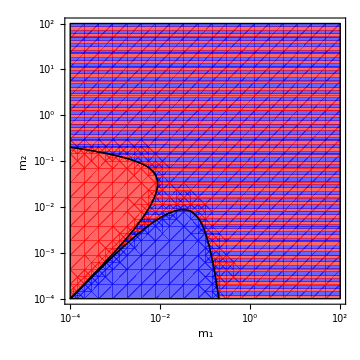

```mathematica
Show[n1wins,n2wins,fc,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

#### f) α12=α21=1.5

```mathematica
α12=α21=1.5;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
op=1;
```

```mathematica
(* 163 s  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 203 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* X s *)
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

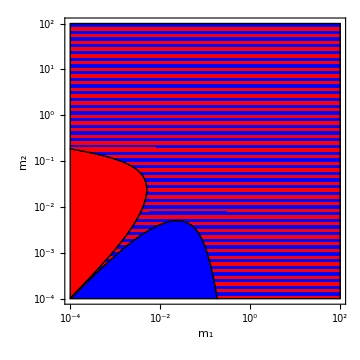

```mathematica
Show[n1wins,n2wins,fc,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

```mathematica
op=0.6;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 287 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-4,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* X s *)
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,2},{m2p,-4,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
Show[n1wins,n2wins,fc,FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

-Graphics-

### Fig S2 — m1-m2, equal α, e=0.01

```mathematica
r1=r2=1;
k1=k2=50;
e=0.01;
Setnmax[2k1,2k2]
```

```mathematica
Clear[m1,m2]
```

```mathematica
ClearCache[λ10,λ20]
```

```mathematica
λ10[m1in_?NumericQ]:=(m1=m1in;NrInOut1[ϵ]/ϵ);
λ20[m2in_?NumericQ]:=(m2=m2in;NrInOut2[ϵ]/ϵ);
```

```mathematica
λ10[10^-3]
```

4.57838

```mathematica
Clear[m1,m2];
LogLogPlot[{λ10[m1i],1},{m1i,10^-4,10^3},PlotRange->All]
LogLogPlot[{λ20[m2i],1},{m2i,10^-4,10^3},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
FindRoot[λ10[10^m1p]==1,{m1p,-3}]
```

{m1p→-3.66143}

```mathematica
λ12[m1in_?NumericQ,m2in_?NumericQ]:=λ12[m1in,m2in]=({m1,m2}={m1in,m2in};Inv1[nr2/.Eq2]);
λ21[m1in_?NumericQ,m2in_?NumericQ]:=λ21[m1in,m2in]=({m1,m2}={m1in,m2in};Inv2[nr1/.Eq1]);
```

```mathematica
dx=3/41;
```

#### A) α12=α21=0.9

```mathematica
α12=α21=0.9;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
op=1;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 312 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 116.5s *)
coex=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]>1,{m1p,-3.6614287292541534,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
Show[n1wins,n2wins,coex,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

-Graphics-

```mathematica
op=0.6;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 287 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 116.5s *)
coex=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]>1,{m1p,-3.6614287292541534,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
Show[n1wins,n2wins,coex,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

-Graphics-

#### B) α12=α21=0.99

```mathematica
α12=α21=0.99;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
op=1;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 312 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 116.5s *)
coex=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]>1,{m1p,-3.6614287292541534,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
Show[n1wins,n2wins,coex,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

-Graphics-

```mathematica
op=0.6;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 287 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 116.5s *)
coex=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]>1,{m1p,-3.6614287292541534,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
Show[n1wins,n2wins,coex,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

-Graphics-

#### C) α12=α21=1

```mathematica
α12=α21=1;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
op=1;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 312 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
Show[n1wins,n2wins,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

-Graphics-

```mathematica
op=0.6;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 287 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
Show[n1wins,n2wins,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

-Graphics-

#### D) α12=α21=1.01

```mathematica
α12=α21=1.01;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
op=1;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 312 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* X s *)
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-3.6614287292541534,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
Show[n1wins,n2wins,fc,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

-Graphics-

```mathematica
op=0.6;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 287 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* X s *)
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-3.6614287292541534,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
Show[n1wins,n2wins,fc,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

-Graphics-

#### E) α12=α21=1.1

```mathematica
α12=α21=1.1;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
op=1;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 312 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* X s *)
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-3.6614287292541534,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
Show[n1wins,n2wins,fc,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

-Graphics-

```mathematica
op=0.6;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 287 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* X s *)
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-3.6614287292541534,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
Show[n1wins,n2wins,fc,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

-Graphics-

#### F) α12=α21=1.5

```mathematica
α12=α21=1.5;
```

```mathematica
ClearCache[λ12,λ21];
Clear[m1,m2]
```

```mathematica
op=1;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 287 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* X s *)
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-3.6614287292541534,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
Show[n1wins,n2wins,fc,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

-Graphics-

```mathematica
op=0.6;
```

```mathematica
(* Xs  *)
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-4,2},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 287 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,2},{m2p,-3.6614287292541534,2},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* X s *)
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-3.6614287292541534,2},{m2p,-3.6614287292541534,2},Mesh->{Table[x,{x,-4,2,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
Show[n1wins,n2wins,fc,Graphics[{Black,EdgeForm[Thick],Rectangle[{-4,-4},{-3.66,-3.66}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},BoundaryStyle->Directive[Black,Thick],ImageSize->Medium,PlotRange->{{-4,2},{-4,2}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-4,2}],None},{Table[{x,Superscript["10",x]},{x,-4,2}],None}}]
```

-Graphics-

### Fig 8 — Invasion dynamics w/ FORTRAN

Try either RunSim (VODE) or RunSimLSODES (LSODES).

#### A) α=1.1, m1=0.01, m2=0.002

```mathematica
mf=25; (* method *)
ml:=n1max+1; (* # lower bands *)
mu:=n1max+1; (* # upper bands *)
rtol=0;
atol=10^-7;

n1max=100;
n2max=100;

Setnmax[n1max,n2max];

r1=1.0;
k1=50;
α12=1.1;
m1=0.01;

r2=1.0;
k2=50;
α21=1.1;
m2=0.002;

e=0.0;
i1=i2=0.0;
```

```mathematica
Clear[nr1,nr2]
```

```mathematica
{Eq1,Eq2}
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{{nr1→48.9789},{nr2→48.9787}}

{2.96923,0.158214}

```mathematica
ϵ=50*10^-3;
invdis1=GetDis[{ϵ,nr2/.Eq2}];
dat=ArrayReshape[invdis1/ϵ,{n2max+1,n1max+1}];
ListPlot3D[dat[[All,2;;]],DataRange->{{0,n1max},{0,n2max}},ViewPoint->{-1.8,-2.2,1},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},PlotRange->All,PlotStyle->{Opacity[0.2],Gray},
MeshFunctions->{Sqrt[#3]&},Mesh->50,ImageSize->Large,TicksStyle->frametickstyle]
```

-Graphics3D-

```mathematica
pinit[n1_,n2_]:=Chop[ArrayReshape[invdis1,{n2max+1,n1max+1}][[n2+1,n1+1]]];
tmax=4000.0;
tskip=2.0;
RunSimLSODES
```

time=38.1243 s

```mathematica
(* n̄ vs t *)
nvst=ListLinePlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},(*AxesLabel->{"t","n̄"},*)PlotRange->{0,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle]
```

-Graphics-

```mathematica
(* n̄ vs t *)
nvst=ListLogPlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},(*AxesLabel->{"t","n̄"},*)PlotRange->{0.001*50,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle,Joined->True]
```

-Graphics-

```mathematica
Clear[nr1,nr2]
```

```mathematica
if1=Interpolation[Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],InterpolationOrder->0];
if2=Interpolation[Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}],InterpolationOrder->0];
nrs={nr1->InterpolationToPiecewise[if1,t],nr2->InterpolationToPiecewise[if2,t]};
```

```mathematica
sol=StochSim[nrs,{n1->10,n2->10},tmax];
PlotDynamics[sol]
```

-Graphics-

```mathematica
Clear[sol];
SeedRandom[1];
Monitor[Do[
sol[x,y]=StochSim[nrs,If[x==3&&y==3,{n1->k1,n2->0},{n1->0,n2->k2}],tmax]
,{x,12},{y,8}]
,{x,y}]
```

```mathematica
frames=Table[
Grid[{
{
Show[nvst,Graphics[{Gray,Line[{{t,0},{t,50}}]}],ImageSize->{400,Automatic}],
Show[Table[DrawPatch[Slice[sol[xc,yc],t],{xc,yc},0.45],{xc,12},{yc,8}],ImageSize->800,ImagePadding->{{0,0},{Automatic,Automatic}}]
},
{
Rasterize[PlotDis[p[Round[t/tskip]],Nrs->GetNr[p[t/tskip]],AxesLabel->{Style["N_1",18],Style["N_2",18]},PlotRange->{-0.0001,0.05}],ImageSize->{400,Automatic},RasterSize->2000],
SpanFromAbove
}
},Spacings->{0,0},(*Frame->All,*)Alignment->{Center,Center}]
,{t,0,tmax}];
```

```mathematica
frames[[-1]]
```

-Graphics- | -Graphics-
-Graphics- |

```mathematica
ListAnimate[frames]
```

```mathematica
Export["invasion_alpha=1.1_m1=0.1_m2=0.002.mp4",frames,FrameRate->25]
```

invasion_alpha=1.1_m1=0.1_m2=0.002.mp4

#### B) α=1.1, m1=0.1, m2=0.002

```mathematica
mf=25; (* method *)
ml:=n1max+1; (* # lower bands *)
mu:=n1max+1; (* # upper bands *)
rtol=0;
atol=10^-7;

n1max=100;
n2max=100;

Setnmax[n1max,n2max];

r1=1.0;
k1=50;
α12=1.1;
m1=0.1;

r2=1.0;
k2=50;
α21=1.1;
m2=0.002;

e=0.0;
i1=i2=0.0;
```

```mathematica
Clear[nr1,nr2]
```

```mathematica
{Eq1,Eq2}
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{{nr1→48.9808},{nr2→48.9787}}

{1.12695,0.0288767}

```mathematica
ϵ=50*10^-3;
invdis1=GetDis[{ϵ,nr2/.Eq2}];
dat=ArrayReshape[invdis1/ϵ,{n2max+1,n1max+1}];
ListPlot3D[dat[[All,2;;]],DataRange->{{0,n1max},{0,n2max}},ViewPoint->{-1.8,-2.2,1},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},PlotRange->All,PlotStyle->{Opacity[0.2],Gray},
MeshFunctions->{Sqrt[#3]&},Mesh->50,ImageSize->Large,TicksStyle->frametickstyle]
```

-Graphics3D-

```mathematica
pinit[n1_,n2_]:=Chop[ArrayReshape[invdis1,{n2max+1,n1max+1}][[n2+1,n1+1]]];
tmax=2000.0;
tskip=2.0;
RunSimLSODES
```

time=40.9576 s

```mathematica
(* n̄ vs t *)
nvst=ListLinePlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},(*AxesLabel->{"t","n̄"},*)PlotRange->{0,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle]
```

-Graphics-

```mathematica
(* n̄ vs t *)
nvst=ListLogPlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},(*AxesLabel->{"t","n̄"},*)PlotRange->{0.001*50,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle,Joined->True]
```

-Graphics-

#### α=1.1, m1=0.01, m2=0.002 – iite

```mathematica
mf=25; (* method *)
ml:=n1max+1; (* # lower bands *)
mu:=n1max+1; (* # upper bands *)
rtol=0;
atol=10^-7;

n1max=100;
n2max=100;

Setnmax[n1max,n2max];

r1=1.0;
k1=50;
α12=1.1;
m1=0.01;

r2=1.0;
k2=50;
α21=1.1;
m2=0.002;

e=0.0;
i1=i2=0.0;
```

```mathematica
Clear[nr1,nr2]
```

```mathematica
{Eq1,Eq2}
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{{nr1→48.9789},{nr2→48.9787}}

{2.96924,0.158214}

```mathematica
ϵ=10^-4;
invdis1=GetDis[{ϵ,nr2/.Eq2}]/ϵ;
dat=ArrayReshape[invdis1,{n2max+1,n1max+1}];
ListPlot3D[dat[[All,2;;]],DataRange->{{0,n1max},{0,n2max}},ViewPoint->{-1.8,-2.2,1},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},PlotRange->All,PlotStyle->{Opacity[0.2],Gray},
MeshFunctions->{Sqrt[#3]&},Mesh->50,ImageSize->Large,TicksStyle->frametickstyle]
```

-Graphics3D-

```mathematica
(* 2 as resident, 1 as invader *)
pinit[n1_,n2_]:=Which[
n1==k1&&n2==0,1./96,
n1==0&&n2==k2,95./96,
True,0];
tmax=3000.0;
tskip=10.0;
RunSimLSODES
```

time=23.3004 s

```mathematica
(* plot patch types vs time *)
ListPlot[Transpose[Table[Transpose[{{t,t,t,t}*tskip,Flatten[Prob2[p[t]]]}],{t,0,tend}]],PlotLegends->{p0,p1,p2,p12},PlotStyle->{Black,Blue,Red,Purple}]
```

-Graphics-

```mathematica
(* n̄ vs t *)
nvst=ListLinePlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},(*AxesLabel->{"t","n̄"},*)PlotRange->{0,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle]
```

-Graphics-

```mathematica
Clear[nr1,nr2]
```

```mathematica
if1=Interpolation[Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],InterpolationOrder->0];
if2=Interpolation[Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}],InterpolationOrder->0];
nrs={nr1->InterpolationToPiecewise[if1,t],nr2->InterpolationToPiecewise[if2,t]};
```

```mathematica
sol=StochSim[nrs,{n1->10,n2->10},3000];
PlotDynamics[sol]
```

-Graphics-

```mathematica
Clear[sol];
SeedRandom[2];
Monitor[Do[
sol[x,y]=StochSim[nrs,If[x==3&&y==3,{n1->k1,n2->0},{n1->0,n2->k2}],3000]
,{x,12},{y,8}]
,{x,y}]
```

```mathematica
frames=Table[
Grid[{
{
Show[nvst,Graphics[{Gray,Line[{{t,0},{t,50}}]}],ImageSize->{400,Automatic}],
Show[Table[DrawPatch[Slice[sol[xc,yc],t],{xc,yc},0.45],{xc,12},{yc,8}],ImageSize->800,ImagePadding->{{0,0},{Automatic,Automatic}}]
},
{
Rasterize[PlotDis[p[Round[t/tskip]],Nrs->GetNr[p[t/tskip]],AxesLabel->{Style["N_1",18],Style["N_2",18]},PlotRange->{-0.0001,0.05}],ImageSize->{400,Automatic},RasterSize->2000],
SpanFromAbove
}
},Spacings->{0,0},(*Frame->All,*)Alignment->{Center,Center}]
,{t,0,tmax,10}];
```

```mathematica
frames[[-1]]
```

-Graphics- | -Graphics-
-Graphics- |

```mathematica
Export["invasion_alpha=1.1_m1=0.01_m2=0.002.mp4",frames,FrameRate->25]
```

invasion_alpha=1.1_m1=0.01_m2=0.002.mp4

#### α=1.1, m1=0.1, m2=0.002 – iite

```mathematica
mf=25; (* method *)
ml:=n1max+1; (* # lower bands *)
mu:=n1max+1; (* # upper bands *)
rtol=0;
atol=10^-7;

n1max=100;
n2max=100;

Setnmax[n1max,n2max];

r1=1.0;
k1=50;
α12=1.1;
m1=0.1;

r2=1.0;
k2=50;
α21=1.1;
m2=0.002;

e=0.0;
i1=i2=0.0;
```

```mathematica
Clear[nr1,nr2]
```

```mathematica
{Eq1,Eq2}
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{{nr1→48.9808},{nr2→48.9787}}

{1.13242,0.0288766}

```mathematica
ϵ=10^-4;
invdis1=GetDis[{ϵ,nr2/.Eq2}]/ϵ;
dat=ArrayReshape[invdis1,{n2max+1,n1max+1}];
ListPlot3D[dat[[All,2;;]],DataRange->{{0,n1max},{0,n2max}},ViewPoint->{-1.8,-2.2,1},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},PlotRange->All,PlotStyle->{Opacity[0.2],Gray},
MeshFunctions->{Sqrt[#3]&},Mesh->50,ImageSize->Large,TicksStyle->frametickstyle]
```

-Graphics3D-

```mathematica
(* 2 as resident, 1 as invader *)
pinit[n1_,n2_]:=Which[
n1==k1&&n2==0,1./96,
n1==0&&n2==k2,95./96,
True,0];
tmax=600.0;
tskip=1.0;
RunSimLSODES
```

time=21.5246 s

```mathematica
(* plot patch types vs time *)
ListPlot[Transpose[Table[Transpose[{{t,t,t,t}*tskip,Flatten[Prob2[p[t]]]}],{t,0,tend}]],PlotLegends->{p0,p1,p2,p12},PlotStyle->{Black,Blue,Red,Purple}]
```

-Graphics-

```mathematica
(* n̄ vs t *)
nvst=ListLinePlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},(*AxesLabel->{"t","n̄"},*)PlotRange->{0,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle]
```

-Graphics-

```mathematica
(* log n̄ vs t *)
nvst=ListLogPlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},(*AxesLabel->{"t","n̄"},*)PlotRange->{0.01*50,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle,Joined->True]
```

-Graphics-

```mathematica
Clear[nr1,nr2]
```

```mathematica
if1=Interpolation[Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],InterpolationOrder->0];
if2=Interpolation[Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}],InterpolationOrder->0];
nrs={nr1->InterpolationToPiecewise[if1,t],nr2->InterpolationToPiecewise[if2,t]};
```

```mathematica
sol=StochSim[nrs,{n1->10,n2->10},tmax];
PlotDynamics[sol]
```

-Graphics-

```mathematica
Clear[sol];
SeedRandom[1];
Monitor[Do[
sol[x,y]=StochSim[nrs,If[x==3&&y==3,{n1->k1,n2->0},{n1->0,n2->k2}],tmax]
,{x,12},{y,8}]
,{x,y}]
```

```mathematica
frames=Table[
Grid[{
{
Show[nvst,Graphics[{Gray,Line[{{t,0},{t,50}}]}],ImageSize->{400,Automatic}],
Show[Table[DrawPatch[Slice[sol[xc,yc],t],{xc,yc},0.45],{xc,12},{yc,8}],ImageSize->800,ImagePadding->{{0,0},{Automatic,Automatic}}]
},
{
Rasterize[PlotDis[p[Round[t/tskip]],Nrs->GetNr[p[t/tskip]],AxesLabel->{Style["N_1",18],Style["N_2",18]},PlotRange->{-0.0001,0.05}],ImageSize->{400,Automatic},RasterSize->2000],
SpanFromAbove
}
},Spacings->{0,0},(*Frame->All,*)Alignment->{Center,Center}]
,{t,0,tmax}];
```

```mathematica
frames[[-1]]
```

-Graphics- | -Graphics-
-Graphics- |

```mathematica
ListAnimate[frames]
```

```mathematica
Export["invasion_alpha=1.1_m1=0.1_m2=0.002.mp4",frames,FrameRate->25]
```

invasion_alpha=1.1_m1=0.1_m2=0.002.mp4

#### α=1.1, m1=0.003, m2=0.002

```mathematica
mf=25; (* method *)
ml:=n1max+1; (* # lower bands *)
mu:=n1max+1; (* # upper bands *)
rtol=0;
atol=10^-7;

n1max=100;
n2max=100;

Setnmax[n1max,n2max];

r1=1.0;
k1=50;
α12=1.1;
m1=0.003;

r2=1.0;
k2=50;
α21=1.1;
m2=0.002;

e=0.0;
i1=i2=0.0;
```

```mathematica
Clear[nr1,nr2]
```

```mathematica
{Eq1,Eq2}
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{{nr1→48.9788},{nr2→48.9787}}

{1.23423,0.563968}

```mathematica
ϵ=10^-4;
invdis1=GetDis[{ϵ,nr2/.Eq2}]/ϵ;
dat=ArrayReshape[invdis1,{n2max+1,n1max+1}];
ListPlot3D[dat[[All,2;;]],DataRange->{{0,n1max},{0,n2max}},ViewPoint->{-1.8,-2.2,1},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},PlotRange->All,PlotStyle->{Opacity[0.2],Gray},
MeshFunctions->{Sqrt[#3]&},Mesh->50,ImageSize->Large,TicksStyle->frametickstyle]
```

-Graphics3D-

```mathematica
(* 2 as resident, 1 as invader *)
pinit[n1_,n2_]:=Which[
n1==k1&&n2==0,1./96,
n1==0&&n2==k2,95./96,
True,0];
tmax=20000.0;
tskip=100.0;
RunSimLSODES
```

time=66.7033 s

```mathematica
(* plot patch types vs time *)
ListPlot[Transpose[Table[Transpose[{{t,t,t,t}*tskip,Flatten[Prob2[p[t]]]}],{t,0,tend}]],PlotLegends->{p0,p1,p2,p12},PlotStyle->{Black,Blue,Red,Purple}]
```

-Graphics-

```mathematica
(* n̄ vs t *)
nvst=ListLinePlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},(*AxesLabel->{"t","n̄"},*)PlotRange->{0,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle]
```

-Graphics-

```mathematica
(* n̄ vs t *)
nvst=ListLinePlot[{Table[{t*tskip,Log10[GetNr[p[t]]⟦1⟧]},{t,0,tend}],Table[{t*tskip,Log10[GetNr[p[t]]⟦2⟧]},{t,0,tend}]},PlotStyle->{Blue,Red},(*AxesLabel->{"t","n̄"},*)(*PlotRange->{0,50},*)PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle]
```

-Graphics-

```mathematica
Clear[nr1,nr2]
```

```mathematica
if1=Interpolation[Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],InterpolationOrder->0];
if2=Interpolation[Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}],InterpolationOrder->0];
nrs={nr1->InterpolationToPiecewise[if1,t],nr2->InterpolationToPiecewise[if2,t]};
```

```mathematica
sol=StochSim[nrs,{n1->10,n2->10},3000];
PlotDynamics[sol]
```

-Graphics-

```mathematica
Clear[sol];
SeedRandom[2];
Monitor[Do[
sol[x,y]=StochSim[nrs,If[x==3&&y==3,{n1->k1,n2->0},{n1->0,n2->k2}],3000]
,{x,12},{y,8}]
,{x,y}]
```

```mathematica
frames=Table[
Grid[{
{
Show[nvst,Graphics[{Gray,Line[{{t,0},{t,50}}]}],ImageSize->{400,Automatic}],
Show[Table[DrawPatch[Slice[sol[xc,yc],t],{xc,yc},0.45],{xc,12},{yc,8}],ImageSize->800,ImagePadding->{{0,0},{Automatic,Automatic}}]
},
{
Rasterize[PlotDis[p[Round[t/tskip]],Nrs->GetNr[p[t/tskip]],AxesLabel->{Style["N_1",18],Style["N_2",18]},PlotRange->{-0.0001,0.05}],ImageSize->{400,Automatic},RasterSize->2000],
SpanFromAbove
}
},Spacings->{0,0},(*Frame->All,*)Alignment->{Center,Center}]
,{t,0,tmax,10}];
```

```mathematica
frames[[-1]]
```

-Graphics- | -Graphics-
-Graphics- |

```mathematica
Export["invasion_alpha=1.1_m1=0.01_m2=0.002.mp4",frames,FrameRate->25]
```

invasion_alpha=1.1_m1=0.01_m2=0.002.mp4

#### α=1.01, m1=0.1, m2=0.05

```mathematica
mf=25; (* method *)
ml:=n1max+1; (* # lower bands *)
mu:=n1max+1; (* # upper bands *)
rtol=0;
atol=10^-7;

n1max=100;
n2max=100;

Setnmax[n1max,n2max];

r1=1.0;
k1=50;
α12=1.01;
m1=0.1;

r2=1.0;
k2=50;
α21=1.01;
m2=0.05;

e=0.0;
i1=i2=0.0;
```

```mathematica
Clear[nr1,nr2]
```

```mathematica
{Eq1,Eq2}
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{{nr1→48.9808},{nr2→48.9798}}

{1.0291,0.772779}

```mathematica
ϵ=10^-4;
invdis1=GetDis[{ϵ,nr2/.Eq2}]/ϵ;
dat=ArrayReshape[invdis1,{n2max+1,n1max+1}];
ListPlot3D[dat[[All,2;;]],DataRange->{{0,n1max},{0,n2max}},ViewPoint->{-1.8,-2.2,1},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},PlotRange->All,PlotStyle->{Opacity[0.2],Gray},
MeshFunctions->{Sqrt[#3]&},Mesh->50,ImageSize->Large,TicksStyle->frametickstyle]
```

-Graphics3D-

```mathematica
(* 2 as resident, 1 as invader *)
pinit[n1_,n2_]:=Which[
n1==k1&&n2==0,1./96,
n1==0&&n2==k2,95./96,
True,0];
tmax=1500.0;
tskip=5.0;
RunSimLSODES
```

time=122.037 s

```mathematica
(* plot patch types vs time *)
ListPlot[Transpose[Table[Transpose[{{t,t,t,t}*tskip,Flatten[Prob2[p[t]]]}],{t,0,tend}]],PlotLegends->{p0,p1,p2,p12},PlotStyle->{Black,Blue,Red,Purple}]
```

-Graphics-

```mathematica
(* n̄ vs t *)
nvst=ListLinePlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},(*AxesLabel->{"t","n̄"},*)PlotRange->{0,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle]
```

-Graphics-

```mathematica
Clear[nr1,nr2]
```

```mathematica
if1=Interpolation[Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],InterpolationOrder->0];
if2=Interpolation[Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}],InterpolationOrder->0];
nrs={nr1->InterpolationToPiecewise[if1,t],nr2->InterpolationToPiecewise[if2,t]};
```

```mathematica
sol=StochSim[nrs,{n1->10,n2->10},tmax];
PlotDynamics[sol]
```

-Graphics-

```mathematica
Clear[sol];
SeedRandom[2];
Monitor[Do[
sol[x,y]=StochSim[nrs,If[x==3&&y==3,{n1->k1,n2->0},{n1->0,n2->k2}],1500]
,{x,12},{y,8}]
,{x,y}]
```

```mathematica
frames=Table[
Grid[{
{
Show[nvst,Graphics[{Gray,Line[{{t,0},{t,50}}]}],ImageSize->{400,Automatic}],
Show[Table[DrawPatch[Slice[sol[xc,yc],t],{xc,yc},0.45],{xc,12},{yc,8}],ImageSize->800,ImagePadding->{{0,0},{Automatic,Automatic}}]
},
{
Rasterize[PlotDis[p[Round[t/tskip]],Nrs->GetNr[p[t/tskip]],AxesLabel->{Style["N_1",18],Style["N_2",18]},PlotRange->{-0.0001,0.05}],ImageSize->{400,Automatic},RasterSize->2000],
SpanFromAbove
}
},Spacings->{0,0},(*Frame->All,*)Alignment->{Center,Center}]
,{t,0,tmax,5}];
```

```mathematica
frames[[-1]]
```

-Graphics- | -Graphics-
-Graphics- |

```mathematica
Export["invasion_alpha=1.01_m1=0.1_m2=0.05.mp4",frames,FrameRate->25]
```

invasion_alpha=1.01_m1=0.1_m2=0.05.mp4

#### α=1.01, m1=1, m2=0.05

```mathematica
mf=25; (* method *)
ml:=n1max+1; (* # lower bands *)
mu:=n1max+1; (* # upper bands *)
rtol=0;
atol=10^-7;

n1max=100;
n2max=100;

Setnmax[n1max,n2max];

r1=1.0;
k1=50;
α12=1.01;
m1=1.0;

r2=1.0;
k2=50;
α21=1.01;
m2=0.05;

e=0.0;
i1=i2=0.0;
```

```mathematica
Clear[nr1,nr2]
```

```mathematica
{Eq1,Eq2}
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{{nr1→48.9898},{nr2→48.9798}}

{1.00046,0.449073}

```mathematica
ϵ=10^-4;
invdis1=GetDis[{ϵ,nr2/.Eq2}]/ϵ;
dat=ArrayReshape[invdis1,{n2max+1,n1max+1}];
ListPlot3D[dat[[All,2;;]],DataRange->{{0,n1max},{0,n2max}},ViewPoint->{-1.8,-2.2,1},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},PlotRange->All,PlotStyle->{Opacity[0.2],Gray},
MeshFunctions->{Sqrt[#3]&},Mesh->50,ImageSize->Large,TicksStyle->frametickstyle]
```

-Graphics3D-

```mathematica
(* 2 as resident, 1 as invader *)
pinit[n1_,n2_]:=Which[
n1==k1&&n2==0,1./96,
n1==0&&n2==k2,95./96,
True,0];
tmax=1500.0;
tskip=5.0;
RunSimLSODES
```

time=422.21 s

```mathematica
(* plot patch types vs time *)
ListPlot[Transpose[Table[Transpose[{{t,t,t,t}*tskip,Flatten[Prob2[p[t]]]}],{t,0,tend}]],PlotLegends->{p0,p1,p2,p12},PlotStyle->{Black,Blue,Red,Purple}]
```

-Graphics-

```mathematica
(* n̄ vs t *)
nvst=ListLinePlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},(*AxesLabel->{"t","n̄"},*)PlotRange->{0,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle]
```

-Graphics-

```mathematica
Clear[nr1,nr2]
```

```mathematica
if1=Interpolation[Table[{t*tskip,Max[0,GetNr[p[t]]⟦1⟧]},{t,0,tend}],InterpolationOrder->0];
if2=Interpolation[Table[{t*tskip,Max[0,GetNr[p[t]]⟦2⟧]},{t,0,tend}],InterpolationOrder->0];
nrs={nr1->InterpolationToPiecewise[if1,t],nr2->InterpolationToPiecewise[if2,t]};
```

```mathematica
sol=StochSim[nrs,{n1->10,n2->10},tmax];
PlotDynamics[sol]
```

-Graphics-

```mathematica
Clear[sol];
SeedRandom[2];
Monitor[Do[
sol[x,y]=StochSim[nrs,If[x==3&&y==3,{n1->k1,n2->0},{n1->0,n2->k2}],1500]
,{x,12},{y,8}]
,{x,y}]
```

```mathematica
frames=Table[
Grid[{
{
Show[nvst,Graphics[{Gray,Line[{{t,0},{t,50}}]}],ImageSize->{400,Automatic}],
Show[Table[DrawPatch[Slice[sol[xc,yc],t],{xc,yc},0.45],{xc,12},{yc,8}],ImageSize->800,ImagePadding->{{0,0},{Automatic,Automatic}}]
},
{
Rasterize[PlotDis[p[Round[t/tskip]],Nrs->GetNr[p[t/tskip]],AxesLabel->{Style["N_1",18],Style["N_2",18]},PlotRange->{-0.0001,0.05}],ImageSize->{400,Automatic},RasterSize->2000],
SpanFromAbove
}
},Spacings->{0,0},(*Frame->All,*)Alignment->{Center,Center}]
,{t,0,tmax,5}];
```

```mathematica
frames[[-1]]
```

-Graphics- | -Graphics-
-Graphics- |

```mathematica
ListAnimate[frames]
```

```mathematica
Export["invasion_alpha=1.01_m1=1_m2=0.05.mp4",frames,FrameRate->25]
```

invasion_alpha=1.01_m1=1_m2=0.05.mp4

#### α=0.99, m1=0.1, m2=0.05

```mathematica
mf=25; (* method *)
ml:=n1max+1; (* # lower bands *)
mu:=n1max+1; (* # upper bands *)
rtol=0;
atol=10^-7;

n1max=100;
n2max=100;

Setnmax[n1max,n2max];

r1=1.0;
k1=50;
α12=0.99;
m1=0.1;

r2=1.0;
k2=50;
α21=0.99;
m2=0.05;

e=0.0;
i1=i2=0.0;
```

```mathematica
Clear[nr1,nr2]
```

```mathematica
{Eq1,Eq2}
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{{nr1→48.9808},{nr2→48.9798}}

{1.16551,0.900316}

```mathematica
ϵ=10^-4;
invdis1=GetDis[{ϵ,nr2/.Eq2}]/ϵ;
dat=ArrayReshape[invdis1,{n2max+1,n1max+1}];
ListPlot3D[dat[[All,2;;]],DataRange->{{0,n1max},{0,n2max}},ViewPoint->{-1.8,-2.2,1},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},PlotRange->All,PlotStyle->{Opacity[0.2],Gray},
MeshFunctions->{Sqrt[#3]&},Mesh->50,ImageSize->Large,TicksStyle->frametickstyle]
```

-Graphics3D-

```mathematica
(* 2 as resident, 1 as invader *)
pinit[n1_,n2_]:=Which[
n1==k1&&n2==0,1./96,
n1==0&&n2==k2,95./96,
True,0];
tmax=1500.0;
tskip=5.0;
RunSimLSODES
```

time=140.585 s

```mathematica
(* plot patch types vs time *)
ListPlot[Transpose[Table[Transpose[{{t,t,t,t}*tskip,Flatten[Prob2[p[t]]]}],{t,0,tend}]],PlotLegends->{p0,p1,p2,p12},PlotStyle->{Black,Blue,Red,Purple}]
```

-Graphics-

```mathematica
(* n̄ vs t *)
nvst=ListLinePlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},(*AxesLabel->{"t","n̄"},*)PlotRange->{0,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle]
```

-Graphics-

```mathematica
Clear[nr1,nr2]
```

```mathematica
if1=Interpolation[Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],InterpolationOrder->0];
if2=Interpolation[Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}],InterpolationOrder->0];
nrs={nr1->InterpolationToPiecewise[if1,t],nr2->InterpolationToPiecewise[if2,t]};
```

```mathematica
sol=StochSim[nrs,{n1->10,n2->10},tmax];
PlotDynamics[sol]
```

-Graphics-

```mathematica
Clear[sol];
SeedRandom[2];
Monitor[Do[
sol[x,y]=StochSim[nrs,If[x==3&&y==3,{n1->k1,n2->0},{n1->0,n2->k2}],1500]
,{x,12},{y,8}]
,{x,y}]
```

```mathematica
frames=Table[
Grid[{
{
Show[nvst,Graphics[{Gray,Line[{{t,0},{t,50}}]}],ImageSize->{400,Automatic}],
Show[Table[DrawPatch[Slice[sol[xc,yc],t],{xc,yc},0.45],{xc,12},{yc,8}],ImageSize->800,ImagePadding->{{0,0},{Automatic,Automatic}}]
},
{
Rasterize[PlotDis[p[Round[t/tskip]],Nrs->GetNr[p[t/tskip]],AxesLabel->{Style["N_1",18],Style["N_2",18]},PlotRange->{-0.0001,0.05}],ImageSize->{400,Automatic},RasterSize->2000],
SpanFromAbove
}
},Spacings->{0,0},(*Frame->All,*)Alignment->{Center,Center}]
,{t,0,tmax,5}];
```

```mathematica
Dynamic[t]
```

```mathematica
frames[[-1]]
```

-Graphics- | -Graphics-
-Graphics- |

```mathematica
ListAnimate[frames]
```

```mathematica
Export["invasion_alpha=0.99_m1=0.1_m2=0.05.mp4",frames,FrameRate->25]
```

invasion_alpha=0.99_m1=0.1_m2=0.05.mp4

#### α=0.99, m1=0.01, m2=0.002

```mathematica
mf=25; (* method *)
ml:=n1max+1; (* # lower bands *)
mu:=n1max+1; (* # upper bands *)
rtol=0;
atol=10^-7;

n1max=100;
n2max=100;

Setnmax[n1max,n2max];

r1=1.0;
k1=50;
α12=0.99;
m1=0.01;

r2=1.0;
k2=50;
α21=0.99;
m2=0.002;

e=0.0;
i1=i2=0.0;
```

```mathematica
Clear[nr1,nr2]
```

```mathematica
{Eq1,Eq2}
{Inv1[nr2/.Eq2],Inv2[nr1/.Eq1]}
```

{{nr1→48.9789},{nr2→48.9787}}

{3.54543,0.28324}

```mathematica
ϵ=10^-6;
invdis1=GetDis[{ϵ,nr2/.Eq2}]/ϵ;
dat=ArrayReshape[invdis1,{n2max+1,n1max+1}];
ListPlot3D[dat[[All,2;;]],DataRange->{{0,n1max},{0,n2max}},ViewPoint->{-1.8,-2.2,1},AxesEdge->{{-1,-1},{-1,-1},{-1,1}},PlotRange->All,PlotStyle->{Opacity[0.2],Gray},
MeshFunctions->{Sqrt[#3]&},Mesh->50,ImageSize->Large,TicksStyle->frametickstyle]
```

-Graphics3D-

```mathematica
(* 2 as resident, 1 as invader *)
pinit[n1_,n2_]:=Which[
n1==k1&&n2==0,1./96,
n1==0&&n2==k2,95./96,
True,0];
tmax=1500.0;
tskip=5.0;
RunSimLSODES
```

time=12.2469 s

```mathematica
(* plot patch types vs time *)
ListPlot[Transpose[Table[Transpose[{{t,t,t,t}*tskip,Flatten[Prob2[p[t]]]}],{t,0,tend}]],PlotLegends->{p0,p1,p2,p12},PlotStyle->{Black,Blue,Red,Purple}]
```

-Graphics-

```mathematica
(* n̄ vs t *)
nvst=ListLinePlot[{Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}]},PlotStyle->{Blue,Red},(*AxesLabel->{"t","n̄"},*)PlotRange->{0,50},PlotRangePadding->Scaled[.02],TicksStyle->frametickstyle]
```

-Graphics-

```mathematica
Clear[nr1,nr2]
```

```mathematica
if1=Interpolation[Table[{t*tskip,GetNr[p[t]]⟦1⟧},{t,0,tend}],InterpolationOrder->0];
if2=Interpolation[Table[{t*tskip,GetNr[p[t]]⟦2⟧},{t,0,tend}],InterpolationOrder->0];
nrs={nr1->InterpolationToPiecewise[if1,t],nr2->InterpolationToPiecewise[if2,t]};
```

```mathematica
sol=StochSim[nrs,{n1->10,n2->10},tmax];
PlotDynamics[sol]
```

-Graphics-

```mathematica
Clear[sol];
SeedRandom[2];
Monitor[Do[
sol[x,y]=StochSim[nrs,If[x==3&&y==3,{n1->k1,n2->0},{n1->0,n2->k2}],1500]
,{x,12},{y,8}]
,{x,y}]
```

```mathematica
frames=Table[
Grid[{
{
Show[nvst,Graphics[{Gray,Line[{{t,0},{t,50}}]}],ImageSize->{400,Automatic}],
Show[Table[DrawPatch[Slice[sol[xc,yc],t],{xc,yc},0.45],{xc,12},{yc,8}],ImageSize->800,ImagePadding->{{0,0},{Automatic,Automatic}}]
},
{
Rasterize[PlotDis[p[Round[t/tskip]],Nrs->GetNr[p[t/tskip]],AxesLabel->{Style["N_1",18],Style["N_2",18]},PlotRange->{-0.0001,0.05}],ImageSize->{400,Automatic},RasterSize->2000],
SpanFromAbove
}
},Spacings->{0,0},(*Frame->All,*)Alignment->{Center,Center}]
,{t,0,tmax,5}];
```

```mathematica
Dynamic[t]
```

```mathematica
frames[[-1]]
```

-Graphics- | -Graphics-
-Graphics- |

```mathematica
ListAnimate[frames]
```

```mathematica
Export["invasion_alpha=0.99_m1=0.01_m2=0.002.mp4",frames,FrameRate->25]
```

invasion_alpha=0.99_m1=0.01_m2=0.002.mp4

### Fig 9 — m1-m2, competition-colonization trade-off (e=0.01)

```mathematica
Clear[e]
```

```mathematica
r1=r2=1;
k1=k2=50;
α12=0.5;α21=2.0;
Setnmax[2k1,2k2]
e=0.01;
```

### A) Outcomes

```mathematica
λ12[m1in_?NumericQ,m2in_?NumericQ]:=λ12[m1in,m2in]=({m1,m2}={m1in,m2in};Inv1[nr2/.Eq2]);
λ21[m1in_?NumericQ,m2in_?NumericQ]:=λ21[m1in,m2in]=({m1,m2}={m1in,m2in};Inv2[nr1/.Eq1]);
```

```mathematica
ClearCache[λ12,λ21]
```

```mathematica
(* 370 s *)
op=1;
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-5,1},{m2p,-5,1},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 220 s *)
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-5,1},{m2p,-5,1},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 1370 s *)
coex=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,-2},{m2p,-3.8,0.6},MaxRecursion->4,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
(* 301 s *)
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,-2},{m2p,0,1},Mesh->{Table[x,{x,-5,1,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
```

```mathematica
Show[n1wins,Graphics[{Black,Rectangle[{-5.02,-5.02},{1,1}]}],n1wins,n2wins,coex,fc,Graphics[{Thick,Dashed,Line[{{-5,-5},{1,1}}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},ImageSize->400,BoundaryStyle->Directive[Black,Thick],PlotRange->{{-5,1},{-5,1}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-5,1}],None},{Table[{x,Superscript["10",x]},{x,-5,1}],None}}]
```

-Graphics-

```mathematica
blank=RegionPlot[1<0,{m1p,-5,1},{m2p,-5,1}];
```

```mathematica
op=0.6;
n1wins=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]<1,{m1p,-5,1},{m2p,-5,1},PlotStyle->Directive[Blue,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
n2wins=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]>1,{m1p,-5,1},{m2p,-5,1},PlotStyle->Directive[Red,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
coex=RegionPlot[λ12[10^m1p,10^m2p]>1&&λ21[10^m1p,10^m2p]>1,{m1p,-4,-2},{m2p,-3.8,0.6},MaxRecursion->4,PlotStyle->Directive[Purple,Opacity[op]],BoundaryStyle->Directive[Black,Thick]];
fc=RegionPlot[λ12[10^m1p,10^m2p]<1&&λ21[10^m1p,10^m2p]<1,{m1p,-4,-2},{m2p,0,1},Mesh->{Table[x,{x,-5,1,dx}]},MeshStyle->None,MeshFunctions->{#2&},MeshShading->{Directive[Blue,Opacity[op]],Directive[Red,Opacity[op]]},BoundaryStyle->Directive[Black,Thick]];
Show[blank,Graphics[{Black,Rectangle[{-5.02,-5.02},{-3.65,-3.65}]}],n1wins,n2wins,coex,fc,Graphics[{Thick,Dashed,Line[{{-5,-5},{1,1}}]}],FrameStyle->Directive[18,Black],FrameLabel->{Style["m_1",21],Style["m_2",21]},ImageSize->400,BoundaryStyle->Directive[Black,Thick],PlotRange->{{-5,1},{-5,1}},FrameTicks->{{Table[{x,Superscript["10",x]},{x,-5,1}],None},{Table[{x,Superscript["10",x]},{x,-5,1}],None}}]
```

-Graphics-

### B-C) m1=10^-3,m2=10^-2

```mathematica
{m1,m2}={0.001,0.01};
eq=Eq12
```

{nr1→29.3598,nr2→14.8057}

```mathematica
WatershedPlot[GetDis[{nr1,nr2}/.eq],PlotRange->{{0,80},{0,80},{0,0.03}},ImageSize->400]
```

-Graphics3D-

```mathematica
sol=StochSim[eq,{n1->0,n2->0},1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

-Graphics-

```mathematica
SquarePie[GetDis[{nr1,nr2}/.eq]]
```

-Graphics-

```mathematica
Clear[sol];
SeedRandom[1];
Monitor[Do[
sol[x,y]=StochSim[eq,rr=RandomReal[];Which[rr<0.1,{n1->0,n2->0},rr<0.7,{n1->k1,n2->0},Else,{n1->0,n2->k2}],1000]
,{x,12},{y,8}]
,{x,y}]
```

```mathematica
frames=Table[
Show[Table[
DrawPatch[Slice[sol[xc,yc],t],{xc,yc},0.45],
{xc,12},{yc,8}],ImageSize->800,PlotLabel->Style[t,24]
],{t,0,600}];
```

```mathematica
frames[[-1]]
```

-Graphics-

```mathematica
Export["comp-col.mp4",frames,FrameRate->25]
```

comp-col.mp4

### D-E) m1=10^-3,m2=10^0

```mathematica
{m1,m2}={0.001,1};
eq=Eq12
```

{nr1→30.5829,nr2→10.9545}

```mathematica
WatershedPlot[GetDis[{nr1,nr2}/.eq],PlotRange->{{0,80},{0,80},{0,0.02}},ImageSize->400]
```

-Graphics3D-

```mathematica
SquarePie[GetDis[{nr1,nr2}/.eq]]
```

-Graphics-

```mathematica
sol=StochSim[eq,{n1->0,n2->0},1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

-Graphics-

```mathematica
Clear[sol];
SeedRandom[1];
Monitor[Do[
sol[x,y]=StochSim[eq,rr=RandomReal[];Which[rr<0.1,{n1->0,n2->0},rr<0.33,{n1->25,n2->0},Else,{n1->5,n2->45}],1000]
,{x,12},{y,8}]
,{x,y}]
```

```mathematica
frames=Table[
Show[Table[
DrawPatch[Slice[sol[xc,yc],t],{xc,yc},0.45],
{xc,12},{yc,8}],ImageSize->800,PlotLabel->Style[t,24]
],{t,0,600}];
```

```mathematica
frames[[-1]]
```

-Graphics-

```mathematica
Export["comp-col2.mp4",frames,FrameRate->25]
```

comp-col2.mp4

## Deterministic Open System (Nasser’s code)

#### Set Model

```mathematica
SetModel[{
Pop[N1]->{Equation:>r1 N1(1-(N1+ α12 N2)/k1)+m1(nr1-N1),Color->Blue},
Pop[N2]->{Equation:>r2 N2(1-(N2+ α21 N1)/k2)+m2(nr2-N2),Color->Red},
Parameters:>{r1>0,r2>0,α12>=0,α21>=0,m1>=0,m2>=0, nr1>0, nr2>0, k1>0, k2>0}
}]
```

## Deterministic model helper functions

#### GetRelativeAbundance

```mathematica
GetRelativeAbundance[eq_]:=(N2/.eq)/((N2/.eq)+(N1/.eq))
```

#### GetCentralEq

```mathematica
GetCentralEq[positiveeqs_]:=Module[{eigs,stable,centraleq},
eigs=EcoEigenvalues/@positiveeqs;
stable=Apply[AllTrue[{##},Negative]&,#]&/@eigs;
centraleq=Which[Count[stable, True]==2, positiveeqs[[Position[stable,False][[1,1]]]],Count[stable, True]==1,positiveeqs[[Position[stable,True][[1]]]]];
Return[centraleq]
]
```

#### GetDist

Looks at all equilibria and splits phase plane into basins of attraction based on central eq

```mathematica
GetDist[positiveeqs_]:=Module[{slope,n1abund,n2abund,tot},
slope=Eigenvectors[EcoJacobian[]/.GetCentralEq[positiveeqs]][[1]];
n1abund=ArcTan[Abs[slope[[2]]],Abs[slope[[1]]]];
n2abund=Pi/2-n1abund;
tot=Total[{n1abund,n2abund}];
Return[Reverse@{n1abund/tot,n2abund/tot}]
]
```

#### PlotSeparatrix

```mathematica
PlotSeparatrix[range_]:=Module[{centraleq,slopecomponents,slope,line,x},
centraleq=Flatten[GetCentralEq[SelectValid[NSolveEcoEq[]]]];
slopecomponents=Eigenvectors[EcoJacobian[]/.centraleq][[1]];
slope=slopecomponents[[2]]/slopecomponents[[1]];
line=slope*(x-N1/.centraleq)+N2/.centraleq;
Show[RegionPlot[{y<line,y>line},{x,0,range},{y,0,range}, PlotStyle->{LightBlue,LightRed},BoundaryStyle->None,BaseStyle->{FontSize->20},FrameLabel->{"N_1","N_2"}],PlotEcoPhasePlane[{N1,0,range},{N2,0,range}]]]
```

```mathematica
r1=1;r2=1;nr1=nr2=k1=k2=50;α12=1.4;α21=1.8;m1=m2=0.001;
```

```mathematica
PlotSeparatrix[60]
```

-Graphics-

#### DeterministicSquarePie

```mathematica
frametickstyle=Directive[Black,16];
DeterministicSquarePie[pf_]:=
SquarePieChart[Values[pf],ChartStyle->(Directive[DeterministicCF[#],EdgeForm[]]&)/@Keys[pf],SectorOrigin->5π/4-π*(-1/.pf),LabelingFunction->None]
```

```mathematica
r1=1;r2=1;nr1=nr2=k1=k2=50;α12=1.4;α21=1.8;m1=m2=0.001;
```

```mathematica
Rasterize[DeterministicSquarePie[DeterministicProbFrac[NSolveEcoEq[]]]]
```

Values::invrl: The argument DeterministicProbFrac[{{N1→49.9125,N2→0.0625703},{N1→0.125888,N2→49.7736},{N1→13.1063,N2→26.4532},{N1→-0.0499303,N2→-0.0499104}}] is not a valid Association or a list of rules.

Keys::invrl: The argument DeterministicProbFrac[{{N1→49.9125,N2→0.0625703},{N1→0.125888,N2→49.7736},{N1→13.1063,N2→26.4532},{N1→-0.0499303,N2→-0.0499104}}] is not a valid Association or a list of rules.

Keys::invrl: The argument Directive[DeterministicCF[DeterministicProbFrac[{{N1→49.9125,N2→0.0625703},{N1→0.125888,N2→49.7736},{N1→13.1063,N2→26.4532},{N1→-0.0499303,N2→-0.0499104}}]],EdgeForm[]] is not a valid Association or a list of rules.

ReplaceAll::reps: {DeterministicProbFrac[{{N1→49.9125,N2→0.0625703},{N1→0.125888,N2→49.7736},{N1→13.1063,N2→26.4532},{N1→-0.0499303,N2→-0.0499104}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

PieChart::ldata: Values[DeterministicProbFrac[{{N1→49.9125,N2→0.0625703},{N1→0.125888,N2→49.7736},{N1→13.1063,N2→26.4532},{N1→-0.0499303,N2→-0.0499104}}]] is not a valid dataset or list of datasets.

-Graphics-

#### DeterministicCF

```mathematica
op=1;
DeterministicCF=Which[
#==-1,Directive[Black,Opacity[op]],
#==0,Directive[Blue,Opacity[op]],
#==1,Directive[Red,Opacity[op]],
Else,Directive[Blend[{Blue,Red},#],Opacity[op]]]&;
```

#### DeterministicProbFrac

```mathematica
cutoff=0;
```

```mathematica
DeterministicProbFrac[eqs_]:=If[AnyTrue[Flatten[{N1,N2}/.SelectEcoStable[SelectValid[eqs]]],#< cutoff&],

Which[Length[SelectEcoStable[SelectValid[eqs]]]==1&&GetDist[SelectValid[eqs]][[1]]>GetDist[SelectValid[eqs]][[2]],{-1-> 0, 0-> 1,1->0},Length[SelectEcoStable[SelectValid[eqs]]]==1&&GetDist[SelectValid[eqs]][[2]]>GetDist[SelectValid[eqs]][[1]],{-1-> 0, 0-> 0,1->1},Length[SelectEcoStable[SelectValid[eqs]]]==2,{-1-> 0, 0-> GetDist[eqs][[1]],1->GetDist[eqs][[2]]}],

{-1-> 0, 0-> 0,1->0 ,Indexed[GetRelativeAbundance/@SelectEcoStable[SelectValid[eqs]],1]->If[Length[SelectEcoStable[SelectValid[eqs]]]==2,GetDist[eqs][[1]],1], If[Length[SelectEcoStable[SelectValid[eqs]]]==2,Indexed[GetRelativeAbundance/@SelectEcoStable[SelectValid[eqs]],2],Indexed[GetRelativeAbundance/@SelectEcoStable[SelectValid[eqs]],1]]->If[Length[SelectEcoStable[SelectValid[eqs]]]==2,GetDist[eqs][[2]],1]}]
```

## Plotting

#### Fig 5C. (m1=m2=0.001, K1=K2=NR1=NR2=50)

```mathematica
r1=1;r2=1;nr1=50;nr2=50;k1=50;k2=50;m1=0.001;m2=0.001;
dα=0.1;
Rasterize[Show[Graphics[Flatten[Table[
    Inset[DeterministicSquarePie[DeterministicProbFrac[NSolveEcoEq[]]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

#### Fig 5B. (m1=m2=0.01, K1=K2=NR1=NR2=50)

```mathematica
r1=1;r2=1;nr1=50;nr2=50;k1=50;k2=50;m1=0.01;m2=0.01;
dα=0.1;
Rasterize[Show[Graphics[Flatten[Table[
    Inset[DeterministicSquarePie[DeterministicProbFrac[NSolveEcoEq[]]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

#### Fig 5C. (m1=m2=0.1, K1=K2=NR1=NR2=50)

```mathematica
r1=1;r2=1;nr1=50;nr2=50;k1=50;k2=50;m1=0.1;m2=0.1;
dα=0.1;
Rasterize[Show[Graphics[Flatten[Table[
    Inset[DeterministicSquarePie[DeterministicProbFrac[NSolveEcoEq[]]],{α12,α21},{0,0},dα-0.01]
   ,{α12,0.0,2.0,dα},{α21,0.0,2.0,dα}],1]
  ],Frame->True,PlotRange->{{-0.05-dα/2,2.05+dα/2},{-0.05-dα/2,2.05+dα/2}},FrameTicksStyle->frametickstyle,FrameTicks->{{{0,0.5,1,1.5,2},None},{{0,0.5,1,1.5,2},None}},FrameLabel->{Style["α_12",21],Style["α_21",21]}],ImageResolution->300]
```

-Graphics-

#### Deterministic M vs. ProbFrac plot

```mathematica
r1=1;r2=1;nr1=nr2=k1=k2=50;α12=1.3;α21=1.8;
```

```mathematica
P1={};
P2={};
P12={};
P21={};
```

```mathematica
range=10^Range[-3,-1,0.05];
Do[m1=m2=i;
pf=DeterministicProbFrac[NSolveEcoEq[]];
If[MemberQ[Keys[pf],0],AppendTo[P1,0/.pf],AppendTo[P1,0.] ];
If[MemberQ[Keys[pf],1],AppendTo[P2,1/.pf] ,AppendTo[P2,0.]];AppendTo[P12,Max[DeleteCases[Keys[pf],a_/;MemberQ[{-1,0,1},a]]]/.pf]; 
AppendTo[P21,Min[DeleteCases[Keys[pf],a_/;MemberQ[{-1,0,1},a]]]/.pf];, 
{i,range}]
```

```mathematica
DetMvsP=ListLinePlot[{Transpose[{range,P2}],Transpose[{range,P1}],Transpose[{range,P12}],Transpose[{range,P21}]},PlotStyle->{Red,Blue,{Darker[Red],Dashed},{Darker[Blue],Dashed}},PlotLabels->{"P2","P1","P12","P21"}, Frame->True,PlotRange->{{10^-3,.1},{0,1.}},ScalingFunctions->{"Log","Linear"}]
```

-Graphics-

#### Plotting separatrix

```mathematica
r1=1;r2=1;nr1=nr2=k1=k2=50;α12=1.6;α21=1.8;m1=m2=0.001;
```

```mathematica
Rasterize[PlotSeparatrix[60]]
```

-Graphics-

#### Stochastic simulations

```mathematica
r1=1;r2=1;nr1=nr2=k1=k2=50;α12=0.7;α21=.65;
e=0;
m1=m2=10^-3;
Setnmax[2k1,2k2]
```

```mathematica
dis=GetDis[{k1,k2}];
PlotDis[dis,Nrs->{k1,k2}]
```

-Graphics3D-

#### K vs. P1 plot (α12=1.2, α21=1.3)

```mathematica
r1=r2=1;
e=0;
m1=m2=10^-3;
α12=1.2;α21=1.3;
```

```mathematica
P1={};
P2={};
P12={};
P21={};
```

```mathematica
range=Range[25,200,1];
```

```mathematica
Do[k1=k2=i;
Setnmax[2 k1,2  k2];dis=GetDis[{k1,k2}];
pf=ProbFrac[dis];If[MemberQ[Keys[pf],0.],AppendTo[P1,0./.pf],AppendTo[P1,0.] ];
If[MemberQ[Keys[pf],1.],AppendTo[P2,1./.pf] ,AppendTo[P2,0.]];AppendTo[P12,Max[DeleteCases[Keys[pf],a_/;MemberQ[{-1,0.,1.},a]]]/.pf]; 
AppendTo[P21,Min[DeleteCases[Keys[pf],a_/;MemberQ[{-1,0.,1.},a]]]/.pf];, 
{i,range}]
```

```mathematica
ListLinePlot[{Transpose[{range,P2}],Transpose[{range,P1}],Transpose[{range,P12}],Transpose[{range,P21}]},PlotStyle->{Red,Blue,{Green,Dashed},{Orange,Dashed}},PlotLabels->{"P_2","P_1","P12","P21"}, Frame->True,PlotRange->{{25,200},{0,1}},GridLines->{{{40,{Black,Thick}},{150,{Black,Thick}}},{{0.372228883266225,Directive[Red,Dashed,Thick]},{0.6277711167337751,Directive[Blue,Dashed,Thick]}}},LabelStyle->Large, AspectRatio->1]
```

-Graphics-

#### m vs. P1,P2 plot (α12=1.2, α21=1.3)

```mathematica
r1=r2=1;
e=0;
k1=k2=50;
α12=1.3;α21=1.8;
```

```mathematica
P1={};
P2={};
P12={};
P21={};
```

```mathematica
range=10^Range[-3,-1,0.05];
Do[m1=m2=i;
Setnmax[2 k1,2  k2];dis=GetDis[{k1,k2}];
pf=ProbFrac[dis];If[MemberQ[Keys[pf],0.],AppendTo[P1,0./.pf],AppendTo[P1,0.] ];
If[MemberQ[Keys[pf],1.],AppendTo[P2,1./.pf] ,AppendTo[P2,0.]];AppendTo[P12,Max[DeleteCases[Keys[pf],a_/;MemberQ[{-1,0.,1.},a]]]/.pf]; 
AppendTo[P21,Min[DeleteCases[Keys[pf],a_/;MemberQ[{-1,0.,1.},a]]]/.pf];, 
{i,range}]
```

```mathematica
StochMvsP=ListLinePlot[{Transpose[{range,P2}],Transpose[{range,P1}],Transpose[{range,P12}],Transpose[{range,P21}]},PlotStyle->{Red,Blue,{Darker[Red]},{Darker[Blue]}},PlotLabels->{"P2","P1","P12","P21"}, Frame->True,PlotRange->{{10^-3,.1},{0,1}},ScalingFunctions->{"Log","Linear"}]
```

-Graphics-

```mathematica
Show[DetMvsP,StochMvsP]
```

-Graphics-

#### stochsim

```mathematica
r1=r2=1;
e=0;
m1=m2=10^-3;
α12=1.2;α21=1.3;
k1=k2=10;
```

```mathematica
sol=StochSim[{nr1->k1,nr2->k2},{n1->k1/5,n2->k2},1000];
PlotDynamics[sol,PlotPoints->400,PlotRange->Automatic,AxesLabel->None,ImageSize->340,TicksStyle->frametickstyle,LineStyles->Thickness[0.003]]
```

-Graphics-

#### Color bar legend

```mathematica
Rasterize@BarLegend[{DeterministicCF,{0,1}},LabelStyle->Directive[Black, 16],Method->{TicksStyle->{Black,Thickness[0.004]},FrameStyle->Directive[Thickness[0.005],Black]},LegendLayout->"Row"]
```

-Graphics-

```mathematica
Plot[Sin[x],{x,0,10},TicksStyle->Directive[Orange,12]]
```

#### Mean first passage time function + plot

```mathematica
TMNorm[k1_,k2_]:=Module[{DiagNorm, DiagNormMatrix, TMZeroDiag},
DiagNorm=-Total[TM[k1,k2]-DiagonalMatrix[Diagonal@TM[k1,k2]]];
DiagNormMatrix=SparseArray[Band[{1,1}]->DiagNorm,Dimensions[TM[k1,k2]]] ;
TMZeroDiag=SparseArray[TM[k1,k2]-DiagonalMatrix[Diagonal[TM[k1,k2]]]];
Return[TMZeroDiag+DiagNormMatrix];
]
```

```mathematica
GetDisNorm[{nr1_,nr2_}]:=Module[{vec},
vec=Eigenvectors[TMNorm[nr1,nr2],-1,Method->"Arnoldi"]⟦1⟧;
vec/=Total[vec]
];
```

```mathematica
(*Calculates MFPT*)
```

```mathematica
MFPT[{nr1_,nr2_},{n1i_,n2i_}->{n1f_,n2f_}]:=LinearSolve[DeleteRowAndColumn[Transpose[TMNorm[k1,k2]],(n1f+1)+n2f*(n1max+1)],ConstantArray[-1,Dimensions[TM[k1,k2]-1][[1]]-1]][[n1i+1+n2i*(n1max+1)]]
```

WITH NORMALIZATION

```mathematica
r1=r2=1;
e=0;
m1=m2=10^-3;
α12=1.2;α21=1.3;
```

```mathematica
k2tok1norm=Table[k1=k2=i;
Setnmax[2k1,2k2];MFPT[{k1,k2},{0,k2}->{k1,0}],{i,25,200,2}];
```

```mathematica
k1tok2norm=Table[k1=k2=i;
Setnmax[2k1,2k2];MFPT[{k1,k2},{k1,0}->{0,k2}],{i,25,200,2}];
```

```mathematica
ListLinePlot[{Transpose[{Range[25,200,2],k2tok1norm}],Transpose[{Range[25,200,2],k1tok2norm}]},AxesLabel->{"K","MFPT"},PlotStyle->{Darker[Red],Darker[Blue]}, Frame->True,PlotRange->{{25,200},All},GridLines->{{{40,Directive[Black,Thick]},{150,Directive[Black,Thick]}},{}},LabelStyle->Large, AspectRatio->1,ScalingFunctions->{"Linear","Log10"},PlotLabels->{"T_K_2","T_K_1"}]
```

-Graphics-

```mathematica
(*Testing with built in Mathematica function*)
```

```mathematica
k1=k2=20;
```

```mathematica
Setnmax[2k1,2k2];
```

```mathematica
𝒫=ContinuousMarkovProcess[SparseArray[{k1+1->1},Dimensions[TMNorm[k1,k2]][[1]]],Transpose@TMNorm[k1,k2]];
```

ContinuousMarkovProcess::cmnorm: The transition rate matrix had some row sums that were not 0, so the diagonal element for those rows has been set to the negative sum of the remaining row elements.

```mathematica
Mean[FirstPassageTimeDistribution[𝒫,(0+1)+k2*(n1max+1)]]
```

2539.47

```mathematica
MFPT[{k1,k2},{k1,0}->{0,k2}]
```

2539.47